# Defect Modular Bootstrap

## When the modular matrix has degeneracies modular bootstrap can only do so much to predict the the topological lines of the theory. Here we use a version of Breadth First Search to resolve the ambiguities.

## Modular Bootstrap

We will do this example on the folded Tricritical Ising CFT, but the parameters will be documented so that one can change them.

### Defining Folded Tricritical Ising Modular Data

```mathematica
(* Autosave because I've been burnt before *)
Get[FileNameJoin[{NotebookDirectory[],"math4ti2.m"}]];

(* A Timing Function *)
SetAttributes[Time,HoldFirst]
Time[x_]:=With[{res=AbsoluteTiming[x]},Echo[res[[1]],"Time: "];res[[2]]];

(* Define Tricritical Ising Parameters *)
FoldedMinimalModularData[p_:5,pp_:4]:= Module[
{cv,hv,sv,tv,H,i,ho,t,sMaker,s,nH,HIndex,svMat,tv2,twist},
cv=1-6(p-pp)^2/(p pp);(*//Echo[#,"c = "]&;*)
hv[r_,s_]:=hv[r,s]=((p r - pp s)^2-(p - pp)^2)/(4 p pp);
sv[a_,b_]:=sv[a,b]=2 (2/(p pp))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/pp a[[1]] b[[1]]]Sin[π pp/p a[[2]] b[[2]]] ;
tv[a_,e_:1]:=tv[a,e]=ⅇ^(2 π ⅈ e(hv[a[[1]],a[[2]]]-cv/24));
H=Join[Flatten[Table[{r, s}, {r, 1, Floor[(pp-1)/2]}, {s, 1, p-1}], 1], If[EvenQ[pp], Table[{pp/2, s}, {s, 1, Floor[(p-1)/2]}], {}]];

(* Labels of folded Minimal Model primaries under the fixed point chiral algebra *)
i=({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^#}& /@Range[2,2Length[H]+1])~Join~({#[[1]],#[[2]],0}&/@Subsets[H,{2}])~Join~({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^# 2}& /@Range[2,2Length[H]+1]);

(* Their Conformal Weights *)
ho[a_]:=ho[a]=(hv@@(a[[1]])+hv@@(a[[2]])+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@a[[1]])/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;
Echo[ho/@i];

(* Modular T-Matrix *)
t=DiagonalMatrix[Exp[2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;

(*── Precomputed sv/tv tables for H×H ──────────────────────────────*)
nH=Length[H];
HIndex=AssociationThread[H->Range[nH]];
svMat=Table[sv[H[[a]],H[[b]]],{a,nH},{b,nH}];
tv2=Table[tv[H[[a]]]^2,{a,nH}];
twist[a1_,b1_]:=twist[a1,b1]=svMat[[HIndex[a1]]].(tv2*svMat[[All,HIndex[b1]]]);

(* This is the ugliest way I can write down the s-matrix of this thing *)
sMaker[a_,b_]:=sMaker[a,b]=Module[
{a1=a[[1]],a2=a[[2]],a3=a[[3]],b1=b[[1]],b2=b[[2]],b3=b[[3]]},
Which[a3==0&&b3==0,sv[a1,b1] sv[a2,b2]+sv[a1,b2] sv[a2,b1],
a3==0&&Abs[b3]==1,sv[a1,b1] sv[a2,b1],
Abs[a3]==1&&b3==0,sv[a1,b1] sv[a1,b2],
Abs[a3]==1&&Abs[b3]==1,1/2 sv[a1,b1]^2,
Abs[a3]==1&&Abs[b3]==2,1/2 a3 sv[a1,b1],
Abs[a3]==2&&Abs[b3]==1,1/2 b3 sv[a1,b1],
Abs[a3]==2&&Abs[b3]==2,1/8 a3 b3 twist[a1,b1] Exp[π ⅈ (hv@@a1+hv@@b1-cv/12)],
True,0]
];

s=Simplify[Array[sMaker[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}],ComplexityFunction->LeafCount];
{s,t,i,svMat}
];
{s,t,i,sv}=(Clear[s,t,i];FoldedMinimalModularData[5,4])//Time;

(* Modular Mass Matrix *)
z=Outer[(KroneckerDelta[#1,#2] + KroneckerDelta[#1[[1]],#2[[1]]]KroneckerDelta[#1[[2]],#2[[2]]]KroneckerDelta[#1[[3]],-#2[[3]]])(1-KroneckerDelta[Abs[#1[[3]]],2])(1-KroneckerDelta[Abs[#2[[3]]],2])&,i,i,1];
s=Get@FileNameJoin[{NotebookDirectory[],"mS.m"}]//FullSimplify;
z=Get@FileNameJoin[{NotebookDirectory[],"mM.m"}];
(*z=IdentityMatrix[Length@sv];*)
MatrixPlot[z,PlotLabel->"Modular Mass Matrix z"]
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

{0,2,1/5,6/5,6/5,11/5,3,4,7/8,15/8,3/40,43/40,1/10,3/5,3/2,7/16,3/80,7/10,8/5,43/80,11/80,21/10,83/80,51/80,31/16,123/80,19/40,7/160,247/160,3/32,19/32,11/32,27/32,127/160,207/160,21/80,61/80,1/16,9/16}

Time:   0.832694

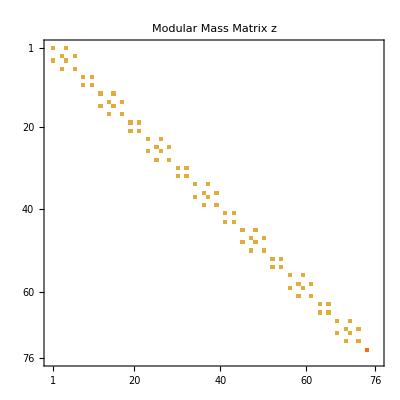

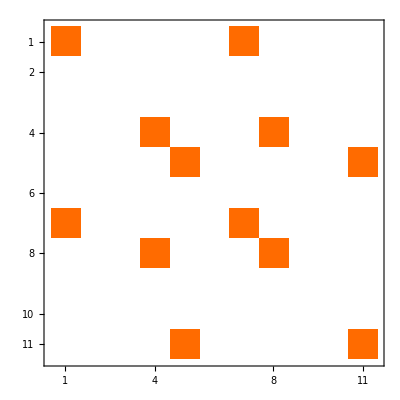

```mathematica
SMatrix[k_]:=Module[{n=k+2},Table[Sqrt[2/n] Sin[Pi (a+1)(b+1)/n],{a,0,k},{b,0,k}]];
ETypeInvariant[k_]:=Module[{M=Table[0,{k+1},{k+1}]},(* |chi_0+chi_6|^2*)M[[1,1]]+=1;M[[1,7]]+=1;
M[[7,1]]+=1;M[[7,7]]+=1;
(* |chi_4+chi_10|^2*)M[[5,5]]+=1;M[[5,11]]+=1;
M[[11,5]]+=1;M[[11,11]]+=1;
(* |chi_3+chi_7|^2*)M[[4,4]]+=1;M[[4,8]]+=1;
M[[8,4]]+=1;M[[8,8]]+=1;
M];
(*s=SMatrix[10];
z=ETypeInvariant[10];
z//MatrixPlot*)
```

### Obtaining Modular Bootstrap Equations

Time:   1.19891

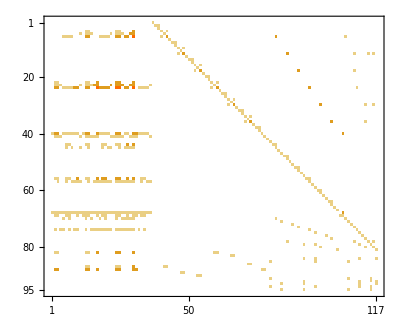

Time:   9.39727

(1. | 1. | 1. | 1. | 2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | 2.68999 | 2.68999 | 2.68999 | 2.68999 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 3.23607 | 3.23607 | 3.23607 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | 3.73205 | 3.73205 | 3.73205 | 3.73205 | 4.3525 | 4.3525 | 4.3525 | 4.3525 | 5.23607 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | 7.3492 | 7.3492 | 7.4641 | 8.8411 | 8.8411 | 8.8411 | 8.8411 | 8.9282 | 9.77064 | 9.77064 | 9.77064 | 9.77064 | 10.0392 | 10.0392 | 10.0392 | 10.0392 | 11.8913 | 11.8913 | 12.0084 | 12.0084 | 12.0772 | 12.0772 | 12.0772 | 13.5027 | 13.5027 | 13.5027 | 13.5027 | 14.4461 | 16.2438 | 16.2438 | 16.2438 | 16.2438 | 19.43 | 19.43 | 19.5413 | 19.5413 | 19.5413 | 23.3743
1. | 1. | 1. | 1. | 2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | 2.68999 | 2.68999 | 2.68999 | 2.68999 | -0.732051 | -0.732051 | -0.732051 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | -0.732051 | 3.23607 | 3.23607 | 3.23607 | -0.984606 | -0.984606 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | -0.984606 | -0.984606 | -1. | -1. | -1. | -1. | 4.3525 | 4.3525 | 4.3525 | 4.3525 | 5.23607 | -1.59313 | -1.59313 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | -1.59313 | -1.59313 | -1.91653 | -1.91653 | -1.91653 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | -1.91653 | -1.96921 | 7.3492 | -2. | -2.36897 | 8.8411 | 8.8411 | -2.36897 | 2. | -2.61803 | -2.61803 | -2.61803 | -2.61803 | -2.68999 | -2.68999 | -2.68999 | -2.68999 | -3.18625 | 11.8913 | 2.68999 | 2.68999 | -3.23607 | -3.23607 | -3.23607 | -3.61803 | -3.61803 | -3.61803 | -3.61803 | 3.23607 | -4.3525 | -4.3525 | -4.3525 | -4.3525 | 4.3525 | 4.3525 | -5.23607 | -5.23607 | -5.23607 | 5.23607
1. | 1. | 1. | 1. | -2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | -2.68999 | 2.68999 | 2.68999 | -2.68999 | -0.732051 | 0.732051 | -0.732051 | -0.732051 | 0.732051 | -0.732051 | 0.732051 | 0.732051 | 3.23607 | 3.23607 | -3.23607 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | 0.267949 | 0.267949 | 0.267949 | 0.267949 | -4.3525 | 4.3525 | 4.3525 | -4.3525 | -5.23607 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | -1.91653 | 1.91653 | -1.91653 | -1.91653 | 1.91653 | -1.91653 | 1.91653 | 1.91653 | -1.96921 | -1.96921 | -0.535898 | -2.36897 | -2.36897 | 2.36897 | 2.36897 | 4.9282 | 0.7015 | 0.7015 | 0.7015 | 0.7015 | -0.720782 | 0.720782 | -0.720782 | 0.720782 | -3.18625 | -3.18625 | 6.62842 | 6.62842 | 0.867102 | -0.867102 | 0.867102 | 0.969449 | 0.969449 | 0.969449 | 0.969449 | 7.974 | -1.16625 | 1.16625 | -1.16625 | 1.16625 | 10.725 | 10.725 | -1.403 | 1.403 | 1.403 | 12.9022
1. | 1. | 1. | 1. | -2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | -2.68999 | 2.68999 | 2.68999 | -2.68999 | 2.73205 | -2.73205 | 2.73205 | -0.732051 | 0.732051 | -0.732051 | 0.732051 | -2.73205 | 3.23607 | 3.23607 | -3.23607 | -3.6746 | -3.6746 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | -3.6746 | -3.6746 | -1. | -1. | -1. | -1. | -4.3525 | 4.3525 | 4.3525 | -4.3525 | -5.23607 | -5.94563 | -5.94563 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | -5.94563 | -5.94563 | 7.1526 | -7.1526 | 7.1526 | -1.91653 | 1.91653 | -1.91653 | 1.91653 | -7.1526 | 7.3492 | -1.96921 | 2. | 8.8411 | -2.36897 | 2.36897 | -8.8411 | -2. | -2.61803 | -2.61803 | -2.61803 | -2.61803 | 2.68999 | -2.68999 | 2.68999 | -2.68999 | 11.8913 | -3.18625 | -2.68999 | -2.68999 | -3.23607 | 3.23607 | -3.23607 | -3.61803 | -3.61803 | -3.61803 | -3.61803 | -3.23607 | 4.3525 | -4.3525 | 4.3525 | -4.3525 | -4.3525 | -4.3525 | 5.23607 | -5.23607 | -5.23607 | -5.23607
1. | 1. | 1. | 1. | 2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | 2.68999 | 2.68999 | 2.68999 | 2.68999 | 2.73205 | 2.73205 | 2.73205 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | 2.73205 | 3.23607 | 3.23607 | 3.23607 | 3.6746 | 3.6746 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | 3.6746 | 3.6746 | -1. | -1. | -1. | -1. | 4.3525 | 4.3525 | 4.3525 | 4.3525 | 5.23607 | 5.94563 | 5.94563 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | 5.94563 | 5.94563 | 7.1526 | 7.1526 | 7.1526 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | 7.1526 | 7.3492 | -1.96921 | -2. | 8.8411 | -2.36897 | -2.36897 | 8.8411 | 2. | -2.61803 | -2.61803 | -2.61803 | -2.61803 | -2.68999 | -2.68999 | -2.68999 | -2.68999 | 11.8913 | -3.18625 | 2.68999 | 2.68999 | -3.23607 | -3.23607 | -3.23607 | -3.61803 | -3.61803 | -3.61803 | -3.61803 | 3.23607 | -4.3525 | -4.3525 | -4.3525 | -4.3525 | 4.3525 | 4.3525 | -5.23607 | -5.23607 | -5.23607 | 5.23607
1. | 1. | 1. | 1. | 2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | 2.68999 | 2.68999 | 2.68999 | 2.68999 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | 3.23607 | 3.23607 | 3.23607 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | 0.267949 | 0.267949 | 0.267949 | 0.267949 | 4.3525 | 4.3525 | 4.3525 | 4.3525 | 5.23607 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | -1.96921 | -1.96921 | 0.535898 | -2.36897 | -2.36897 | -2.36897 | -2.36897 | -4.9282 | 0.7015 | 0.7015 | 0.7015 | 0.7015 | 0.720782 | 0.720782 | 0.720782 | 0.720782 | -3.18625 | -3.18625 | -6.62842 | -6.62842 | 0.867102 | 0.867102 | 0.867102 | 0.969449 | 0.969449 | 0.969449 | 0.969449 | -7.974 | 1.16625 | 1.16625 | 1.16625 | 1.16625 | -10.725 | -10.725 | 1.403 | 1.403 | 1.403 | -12.9022
1. | 1. | 1. | 1. | -2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | -2.68999 | 2.68999 | 2.68999 | -2.68999 | -0.732051 | 0.732051 | -0.732051 | 2.73205 | -2.73205 | 2.73205 | -2.73205 | 0.732051 | 3.23607 | 3.23607 | -3.23607 | 0.984606 | 0.984606 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | 0.984606 | 0.984606 | -1. | -1. | -1. | -1. | -4.3525 | 4.3525 | 4.3525 | -4.3525 | -5.23607 | 1.59313 | 1.59313 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | 1.59313 | 1.59313 | -1.91653 | 1.91653 | -1.91653 | 7.1526 | -7.1526 | 7.1526 | -7.1526 | 1.91653 | -1.96921 | 7.3492 | 2. | -2.36897 | 8.8411 | -8.8411 | 2.36897 | -2. | -2.61803 | -2.61803 | -2.61803 | -2.61803 | 2.68999 | -2.68999 | 2.68999 | -2.68999 | -3.18625 | 11.8913 | -2.68999 | -2.68999 | -3.23607 | 3.23607 | -3.23607 | -3.61803 | -3.61803 | -3.61803 | -3.61803 | -3.23607 | 4.3525 | -4.3525 | 4.3525 | -4.3525 | -4.3525 | -4.3525 | 5.23607 | -5.23607 | -5.23607 | -5.23607
1. | 1. | 1. | 1. | -2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | -2.68999 | 2.68999 | 2.68999 | -2.68999 | 2.73205 | -2.73205 | 2.73205 | 2.73205 | -2.73205 | 2.73205 | -2.73205 | -2.73205 | 3.23607 | 3.23607 | -3.23607 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | 3.73205 | 3.73205 | 3.73205 | 3.73205 | -4.3525 | 4.3525 | 4.3525 | -4.3525 | -5.23607 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | 7.1526 | -7.1526 | 7.1526 | 7.1526 | -7.1526 | 7.1526 | -7.1526 | -7.1526 | 7.3492 | 7.3492 | -7.4641 | 8.8411 | 8.8411 | -8.8411 | -8.8411 | -8.9282 | 9.77064 | 9.77064 | 9.77064 | 9.77064 | -10.0392 | 10.0392 | -10.0392 | 10.0392 | 11.8913 | 11.8913 | -12.0084 | -12.0084 | 12.0772 | -12.0772 | 12.0772 | 13.5027 | 13.5027 | 13.5027 | 13.5027 | -14.4461 | -16.2438 | 16.2438 | -16.2438 | 16.2438 | -19.43 | -19.43 | -19.5413 | 19.5413 | 19.5413 | -23.3743
1. | -1. | -1. | 1. | 0 | 2.61803 | -2.61803 | -2.61803 | 2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.23607 | -3.23607 | 0 | 1.90211 | -1.90211 | -1.90211 | 1.90211 | -1.90211 | 1.90211 | -1.90211 | 1.90211 | -1. | 1. | -1. | 1. | 0 | 0 | 0 | 0 | 0 | 3.07768 | -3.07768 | -3.07768 | 3.07768 | -3.07768 | 3.07768 | -3.07768 | 3.07768 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.61803 | 2.61803 | -2.61803 | 2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.23607 | 0 | 3.23607 | -0.381966 | -0.381966 | 0.381966 | 0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.23607 | 1.23607 | 0
1. | -1. | -1. | 1. | 0 | 2.61803 | -2.61803 | -2.61803 | 2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.23607 | -3.23607 | 0 | -1.90211 | 1.90211 | -1.90211 | 1.90211 | -1.90211 | 1.90211 | 1.90211 | -1.90211 | 1. | -1. | 1. | -1. | 0 | 0 | 0 | 0 | 0 | -3.07768 | 3.07768 | -3.07768 | 3.07768 | -3.07768 | 3.07768 | 3.07768 | -3.07768 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.61803 | -2.61803 | 2.61803 | -2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.23607 | 0 | -3.23607 | 0.381966 | 0.381966 | -0.381966 | -0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.23607 | -1.23607 | 0
1. | -1. | -1. | 1. | 0 | 2.61803 | -2.61803 | -2.61803 | 2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.23607 | -3.23607 | 0 | 1.90211 | -1.90211 | 1.90211 | -1.90211 | 1.90211 | -1.90211 | -1.90211 | 1.90211 | 1. | -1. | 1. | -1. | 0 | 0 | 0 | 0 | 0 | 3.07768 | -3.07768 | 3.07768 | -3.07768 | 3.07768 | -3.07768 | -3.07768 | 3.07768 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.61803 | -2.61803 | 2.61803 | -2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.23607 | 0 | -3.23607 | 0.381966 | 0.381966 | -0.381966 | -0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.23607 | -1.23607 | 0
1. | -1. | -1. | 1. | 0 | 2.61803 | -2.61803 | -2.61803 | 2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.23607 | -3.23607 | 0 | -1.90211 | 1.90211 | 1.90211 | -1.90211 | 1.90211 | -1.90211 | 1.90211 | -1.90211 | -1. | 1. | -1. | 1. | 0 | 0 | 0 | 0 | 0 | -3.07768 | 3.07768 | 3.07768 | -3.07768 | 3.07768 | -3.07768 | 3.07768 | -3.07768 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.61803 | 2.61803 | -2.61803 | 2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.23607 | 0 | 3.23607 | -0.381966 | -0.381966 | 0.381966 | 0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.23607 | 1.23607 | 0
1. | 1. | 1. | 1. | -2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | 2.68999 | -2.68999 | -2.68999 | 2.68999 | 2.73205 | -2.73205 | 2.73205 | 2.73205 | -2.73205 | 2.73205 | -2.73205 | -2.73205 | 3.23607 | 3.23607 | -3.23607 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | 3.73205 | 3.73205 | 3.73205 | 3.73205 | 4.3525 | -4.3525 | -4.3525 | 4.3525 | -5.23607 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | 7.1526 | -7.1526 | 7.1526 | 7.1526 | -7.1526 | 7.1526 | -7.1526 | -7.1526 | -7.3492 | -7.3492 | -7.4641 | 8.8411 | 8.8411 | -8.8411 | -8.8411 | -8.9282 | 9.77064 | 9.77064 | 9.77064 | 9.77064 | 10.0392 | -10.0392 | 10.0392 | -10.0392 | -11.8913 | -11.8913 | 12.0084 | 12.0084 | 12.0772 | -12.0772 | 12.0772 | 13.5027 | 13.5027 | 13.5027 | 13.5027 | -14.4461 | 16.2438 | -16.2438 | 16.2438 | -16.2438 | 19.43 | 19.43 | -19.5413 | 19.5413 | 19.5413 | -23.3743
1. | 1. | 1. | 1. | -2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | 2.68999 | -2.68999 | -2.68999 | 2.68999 | -0.732051 | 0.732051 | -0.732051 | 2.73205 | -2.73205 | 2.73205 | -2.73205 | 0.732051 | 3.23607 | 3.23607 | -3.23607 | -0.984606 | -0.984606 | 3.6746 | 3.6746 | 3.6746 | 3.6746 | -0.984606 | -0.984606 | -1. | -1. | -1. | -1. | 4.3525 | -4.3525 | -4.3525 | 4.3525 | -5.23607 | -1.59313 | -1.59313 | 5.94563 | 5.94563 | 5.94563 | 5.94563 | -1.59313 | -1.59313 | -1.91653 | 1.91653 | -1.91653 | 7.1526 | -7.1526 | 7.1526 | -7.1526 | 1.91653 | 1.96921 | -7.3492 | 2. | -2.36897 | 8.8411 | -8.8411 | 2.36897 | -2. | -2.61803 | -2.61803 | -2.61803 | -2.61803 | -2.68999 | 2.68999 | -2.68999 | 2.68999 | 3.18625 | -11.8913 | 2.68999 | 2.68999 | -3.23607 | 3.23607 | -3.23607 | -3.61803 | -3.61803 | -3.61803 | -3.61803 | -3.23607 | -4.3525 | 4.3525 | -4.3525 | 4.3525 | 4.3525 | 4.3525 | 5.23607 | -5.23607 | -5.23607 | -5.23607
1. | 1. | 1. | 1. | 2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | -2.68999 | -2.68999 | -2.68999 | -2.68999 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | 3.23607 | 3.23607 | 3.23607 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | 0.267949 | 0.267949 | 0.267949 | 0.267949 | -4.3525 | -4.3525 | -4.3525 | -4.3525 | 5.23607 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | 1.96921 | 1.96921 | 0.535898 | -2.36897 | -2.36897 | -2.36897 | -2.36897 | -4.9282 | 0.7015 | 0.7015 | 0.7015 | 0.7015 | -0.720782 | -0.720782 | -0.720782 | -0.720782 | 3.18625 | 3.18625 | 6.62842 | 6.62842 | 0.867102 | 0.867102 | 0.867102 | 0.969449 | 0.969449 | 0.969449 | 0.969449 | -7.974 | -1.16625 | -1.16625 | -1.16625 | -1.16625 | 10.725 | 10.725 | 1.403 | 1.403 | 1.403 | -12.9022
1. | 1. | 1. | 1. | 2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | -2.68999 | -2.68999 | -2.68999 | -2.68999 | 2.73205 | 2.73205 | 2.73205 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | 2.73205 | 3.23607 | 3.23607 | 3.23607 | -3.6746 | -3.6746 | 0.984606 | 0.984606 | 0.984606 | 0.984606 | -3.6746 | -3.6746 | -1. | -1. | -1. | -1. | -4.3525 | -4.3525 | -4.3525 | -4.3525 | 5.23607 | -5.94563 | -5.94563 | 1.59313 | 1.59313 | 1.59313 | 1.59313 | -5.94563 | -5.94563 | 7.1526 | 7.1526 | 7.1526 | -1.91653 | -1.91653 | -1.91653 | -1.91653 | 7.1526 | -7.3492 | 1.96921 | -2. | 8.8411 | -2.36897 | -2.36897 | 8.8411 | 2. | -2.61803 | -2.61803 | -2.61803 | -2.61803 | 2.68999 | 2.68999 | 2.68999 | 2.68999 | -11.8913 | 3.18625 | -2.68999 | -2.68999 | -3.23607 | -3.23607 | -3.23607 | -3.61803 | -3.61803 | -3.61803 | -3.61803 | 3.23607 | 4.3525 | 4.3525 | 4.3525 | 4.3525 | -4.3525 | -4.3525 | -5.23607 | -5.23607 | -5.23607 | 5.23607
1. | 1. | 1. | 1. | -2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | 2.68999 | -2.68999 | -2.68999 | 2.68999 | 2.73205 | -2.73205 | 2.73205 | -0.732051 | 0.732051 | -0.732051 | 0.732051 | -2.73205 | 3.23607 | 3.23607 | -3.23607 | 3.6746 | 3.6746 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | 3.6746 | 3.6746 | -1. | -1. | -1. | -1. | 4.3525 | -4.3525 | -4.3525 | 4.3525 | -5.23607 | 5.94563 | 5.94563 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | 5.94563 | 5.94563 | 7.1526 | -7.1526 | 7.1526 | -1.91653 | 1.91653 | -1.91653 | 1.91653 | -7.1526 | -7.3492 | 1.96921 | 2. | 8.8411 | -2.36897 | 2.36897 | -8.8411 | -2. | -2.61803 | -2.61803 | -2.61803 | -2.61803 | -2.68999 | 2.68999 | -2.68999 | 2.68999 | -11.8913 | 3.18625 | 2.68999 | 2.68999 | -3.23607 | 3.23607 | -3.23607 | -3.61803 | -3.61803 | -3.61803 | -3.61803 | -3.23607 | -4.3525 | 4.3525 | -4.3525 | 4.3525 | 4.3525 | 4.3525 | 5.23607 | -5.23607 | -5.23607 | -5.23607
1. | 1. | 1. | 1. | -2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | 2.68999 | -2.68999 | -2.68999 | 2.68999 | -0.732051 | 0.732051 | -0.732051 | -0.732051 | 0.732051 | -0.732051 | 0.732051 | 0.732051 | 3.23607 | 3.23607 | -3.23607 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | -0.984606 | 0.267949 | 0.267949 | 0.267949 | 0.267949 | 4.3525 | -4.3525 | -4.3525 | 4.3525 | -5.23607 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | -1.59313 | -1.91653 | 1.91653 | -1.91653 | -1.91653 | 1.91653 | -1.91653 | 1.91653 | 1.91653 | 1.96921 | 1.96921 | -0.535898 | -2.36897 | -2.36897 | 2.36897 | 2.36897 | 4.9282 | 0.7015 | 0.7015 | 0.7015 | 0.7015 | 0.720782 | -0.720782 | 0.720782 | -0.720782 | 3.18625 | 3.18625 | -6.62842 | -6.62842 | 0.867102 | -0.867102 | 0.867102 | 0.969449 | 0.969449 | 0.969449 | 0.969449 | 7.974 | 1.16625 | -1.16625 | 1.16625 | -1.16625 | -10.725 | -10.725 | -1.403 | 1.403 | 1.403 | 12.9022
1. | 1. | 1. | 1. | 2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | -2.68999 | -2.68999 | -2.68999 | -2.68999 | -0.732051 | -0.732051 | -0.732051 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | -0.732051 | 3.23607 | 3.23607 | 3.23607 | 0.984606 | 0.984606 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | 0.984606 | 0.984606 | -1. | -1. | -1. | -1. | -4.3525 | -4.3525 | -4.3525 | -4.3525 | 5.23607 | 1.59313 | 1.59313 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | 1.59313 | 1.59313 | -1.91653 | -1.91653 | -1.91653 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | -1.91653 | 1.96921 | -7.3492 | -2. | -2.36897 | 8.8411 | 8.8411 | -2.36897 | 2. | -2.61803 | -2.61803 | -2.61803 | -2.61803 | 2.68999 | 2.68999 | 2.68999 | 2.68999 | 3.18625 | -11.8913 | -2.68999 | -2.68999 | -3.23607 | -3.23607 | -3.23607 | -3.61803 | -3.61803 | -3.61803 | -3.61803 | 3.23607 | 4.3525 | 4.3525 | 4.3525 | 4.3525 | -4.3525 | -4.3525 | -5.23607 | -5.23607 | -5.23607 | 5.23607
1. | 1. | 1. | 1. | 2. | 2.61803 | 2.61803 | 2.61803 | 2.61803 | -2.68999 | -2.68999 | -2.68999 | -2.68999 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 3.23607 | 3.23607 | 3.23607 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | -3.6746 | 3.73205 | 3.73205 | 3.73205 | 3.73205 | -4.3525 | -4.3525 | -4.3525 | -4.3525 | 5.23607 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | -5.94563 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | 7.1526 | -7.3492 | -7.3492 | 7.4641 | 8.8411 | 8.8411 | 8.8411 | 8.8411 | 8.9282 | 9.77064 | 9.77064 | 9.77064 | 9.77064 | -10.0392 | -10.0392 | -10.0392 | -10.0392 | -11.8913 | -11.8913 | -12.0084 | -12.0084 | 12.0772 | 12.0772 | 12.0772 | 13.5027 | 13.5027 | 13.5027 | 13.5027 | 14.4461 | -16.2438 | -16.2438 | -16.2438 | -16.2438 | -19.43 | -19.43 | 19.5413 | 19.5413 | 19.5413 | 23.3743
1. | -1. | 1. | -1. | 0 | 1.61803 | -1.61803 | 1.61803 | -1.61803 | 0 | 2.28825 | -2.28825 | 0 | 0 | 1.41421 | 0 | 0 | -1.41421 | 0 | 1.41421 | -1.41421 | 0 | 0 | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | -1. | -1. | 1. | 1. | 0 | 1.41421 | -1.41421 | 0 | 0 | 1. | 1. | -1. | -1. | 1. | 1. | -1. | -1. | 0 | 2.28825 | 0 | 0 | -2.28825 | 0 | 2.28825 | -2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | 0 | -2.28825 | 0 | 2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.618034 | 0.618034 | 0.618034 | -0.618034 | 0 | 0 | -1.41421 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | 1.61803 | -1.61803 | 1.61803 | -1.61803 | 0 | 2.28825 | -2.28825 | 0 | 0 | -1.41421 | 0 | 0 | -1.41421 | 0 | 1.41421 | 1.41421 | 0 | 0 | 0 | -1.61803 | -1.61803 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | 1.61803 | 1.61803 | 1. | 1. | -1. | -1. | 0 | 1.41421 | -1.41421 | 0 | 0 | -1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 0 | -2.28825 | 0 | 0 | -2.28825 | 0 | 2.28825 | 2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 0 | 2.28825 | 0 | -2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | 0 | 0 | 1.41421 | 0 | -1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | 1.61803 | -1.61803 | 1.61803 | -1.61803 | 0 | 2.28825 | -2.28825 | 0 | 0 | 1.41421 | 0 | 0 | 1.41421 | 0 | -1.41421 | -1.41421 | 0 | 0 | 0 | 1.61803 | 1.61803 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | -1.61803 | -1.61803 | 1. | 1. | -1. | -1. | 0 | 1.41421 | -1.41421 | 0 | 0 | 1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | 0 | 2.28825 | 0 | 0 | 2.28825 | 0 | -2.28825 | -2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 0 | 2.28825 | 0 | -2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | 0 | 0 | 1.41421 | 0 | -1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | 1.61803 | -1.61803 | 1.61803 | -1.61803 | 0 | 2.28825 | -2.28825 | 0 | 0 | -1.41421 | 0 | 0 | 1.41421 | 0 | -1.41421 | 1.41421 | 0 | 0 | 0 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | -1. | -1. | 1. | 1. | 0 | 1.41421 | -1.41421 | 0 | 0 | -1. | -1. | 1. | 1. | -1. | -1. | 1. | 1. | 0 | -2.28825 | 0 | 0 | 2.28825 | 0 | -2.28825 | 2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | 0 | -2.28825 | 0 | 2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.618034 | 0.618034 | 0.618034 | -0.618034 | 0 | 0 | -1.41421 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 2.28825 | 0 | 0 | -2.28825 | 2.73205 | 0 | -2.73205 | 2.73205 | 0 | -2.73205 | 0 | 0 | 0 | 0 | 0 | 3.1258 | -3.1258 | 3.1258 | -3.1258 | -3.1258 | 3.1258 | 3.1258 | -3.1258 | 3.73205 | -3.73205 | -3.73205 | 3.73205 | 1.41421 | 0 | 0 | -1.41421 | 0 | 1.93185 | -1.93185 | 1.93185 | -1.93185 | -1.93185 | 1.93185 | 1.93185 | -1.93185 | 4.42055 | 0 | -4.42055 | 4.42055 | 0 | -4.42055 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.03859 | -6.03859 | -6.03859 | 6.03859 | 8.53985 | 0 | -8.53985 | 0 | 0 | 0 | 10.215 | -10.215 | 0 | 0 | 0 | -2.30653 | 2.30653 | -2.30653 | 2.30653 | 0 | 5.27792 | 0 | -5.27792 | 0 | 6.31319 | -6.31319 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 2.28825 | 0 | 0 | -2.28825 | -0.732051 | 0 | 0.732051 | 2.73205 | 0 | -2.73205 | 0 | 0 | 0 | 0 | 0 | -0.837556 | 0.837556 | 3.1258 | -3.1258 | -3.1258 | 3.1258 | -0.837556 | 0.837556 | -1. | 1. | 1. | -1. | 1.41421 | 0 | 0 | -1.41421 | 0 | -0.517638 | 0.517638 | 1.93185 | -1.93185 | -1.93185 | 1.93185 | -0.517638 | 0.517638 | -1.18448 | 0 | 1.18448 | 4.42055 | 0 | -4.42055 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | -2.28825 | 0 | 2.28825 | 0 | 0 | 0 | 2.28825 | -2.28825 | 0 | 0 | 0 | 0.618034 | -0.618034 | 0.618034 | -0.618034 | 0 | -1.41421 | 0 | 1.41421 | 0 | 1.41421 | -1.41421 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | -2.28825 | 0 | 0 | 2.28825 | -0.732051 | 0 | 0.732051 | -0.732051 | 0 | 0.732051 | 0 | 0 | 0 | 0 | 0 | 0.837556 | -0.837556 | 0.837556 | -0.837556 | -0.837556 | 0.837556 | 0.837556 | -0.837556 | 0.267949 | -0.267949 | -0.267949 | 0.267949 | -1.41421 | 0 | 0 | 1.41421 | 0 | 0.517638 | -0.517638 | 0.517638 | -0.517638 | -0.517638 | 0.517638 | 0.517638 | -0.517638 | -1.18448 | 0 | 1.18448 | -1.18448 | 0 | 1.18448 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.433551 | -0.433551 | -0.433551 | 0.433551 | -0.613134 | 0 | 0.613134 | 0 | 0 | 0 | 5.63847 | -5.63847 | 0 | 0 | 0 | -0.165602 | 0.165602 | -0.165602 | 0.165602 | 0 | -0.378937 | 0 | 0.378937 | 0 | 3.48477 | -3.48477 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | -2.28825 | 0 | 0 | 2.28825 | 2.73205 | 0 | -2.73205 | -0.732051 | 0 | 0.732051 | 0 | 0 | 0 | 0 | 0 | -3.1258 | 3.1258 | 0.837556 | -0.837556 | -0.837556 | 0.837556 | -3.1258 | 3.1258 | -1. | 1. | 1. | -1. | -1.41421 | 0 | 0 | 1.41421 | 0 | -1.93185 | 1.93185 | 0.517638 | -0.517638 | -0.517638 | 0.517638 | -1.93185 | 1.93185 | 4.42055 | 0 | -4.42055 | -1.18448 | 0 | 1.18448 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | 2.28825 | 0 | -2.28825 | 0 | 0 | 0 | -2.28825 | 2.28825 | 0 | 0 | 0 | 0.618034 | -0.618034 | 0.618034 | -0.618034 | 0 | 1.41421 | 0 | -1.41421 | 0 | -1.41421 | 1.41421 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 2.28825 | 0 | 0 | -2.28825 | 2.73205 | 0 | -2.73205 | -0.732051 | 0 | 0.732051 | 0 | 0 | 0 | 0 | 0 | 3.1258 | -3.1258 | -0.837556 | 0.837556 | 0.837556 | -0.837556 | 3.1258 | -3.1258 | -1. | 1. | 1. | -1. | 1.41421 | 0 | 0 | -1.41421 | 0 | 1.93185 | -1.93185 | -0.517638 | 0.517638 | 0.517638 | -0.517638 | 1.93185 | -1.93185 | 4.42055 | 0 | -4.42055 | -1.18448 | 0 | 1.18448 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | -2.28825 | 0 | 2.28825 | 0 | 0 | 0 | 2.28825 | -2.28825 | 0 | 0 | 0 | 0.618034 | -0.618034 | 0.618034 | -0.618034 | 0 | -1.41421 | 0 | 1.41421 | 0 | 1.41421 | -1.41421 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 2.28825 | 0 | 0 | -2.28825 | -0.732051 | 0 | 0.732051 | -0.732051 | 0 | 0.732051 | 0 | 0 | 0 | 0 | 0 | -0.837556 | 0.837556 | -0.837556 | 0.837556 | 0.837556 | -0.837556 | -0.837556 | 0.837556 | 0.267949 | -0.267949 | -0.267949 | 0.267949 | 1.41421 | 0 | 0 | -1.41421 | 0 | -0.517638 | 0.517638 | -0.517638 | 0.517638 | 0.517638 | -0.517638 | -0.517638 | 0.517638 | -1.18448 | 0 | 1.18448 | -1.18448 | 0 | 1.18448 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.433551 | -0.433551 | -0.433551 | 0.433551 | 0.613134 | 0 | -0.613134 | 0 | 0 | 0 | -5.63847 | 5.63847 | 0 | 0 | 0 | -0.165602 | 0.165602 | -0.165602 | 0.165602 | 0 | 0.378937 | 0 | -0.378937 | 0 | -3.48477 | 3.48477 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | -2.28825 | 0 | 0 | 2.28825 | -0.732051 | 0 | 0.732051 | 2.73205 | 0 | -2.73205 | 0 | 0 | 0 | 0 | 0 | 0.837556 | -0.837556 | -3.1258 | 3.1258 | 3.1258 | -3.1258 | 0.837556 | -0.837556 | -1. | 1. | 1. | -1. | -1.41421 | 0 | 0 | 1.41421 | 0 | 0.517638 | -0.517638 | -1.93185 | 1.93185 | 1.93185 | -1.93185 | 0.517638 | -0.517638 | -1.18448 | 0 | 1.18448 | 4.42055 | 0 | -4.42055 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | 2.28825 | 0 | -2.28825 | 0 | 0 | 0 | -2.28825 | 2.28825 | 0 | 0 | 0 | 0.618034 | -0.618034 | 0.618034 | -0.618034 | 0 | 1.41421 | 0 | -1.41421 | 0 | -1.41421 | 1.41421 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | -2.28825 | 0 | 0 | 2.28825 | 2.73205 | 0 | -2.73205 | 2.73205 | 0 | -2.73205 | 0 | 0 | 0 | 0 | 0 | -3.1258 | 3.1258 | -3.1258 | 3.1258 | 3.1258 | -3.1258 | -3.1258 | 3.1258 | 3.73205 | -3.73205 | -3.73205 | 3.73205 | -1.41421 | 0 | 0 | 1.41421 | 0 | -1.93185 | 1.93185 | -1.93185 | 1.93185 | 1.93185 | -1.93185 | -1.93185 | 1.93185 | 4.42055 | 0 | -4.42055 | 4.42055 | 0 | -4.42055 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.03859 | -6.03859 | -6.03859 | 6.03859 | -8.53985 | 0 | 8.53985 | 0 | 0 | 0 | -10.215 | 10.215 | 0 | 0 | 0 | -2.30653 | 2.30653 | -2.30653 | 2.30653 | 0 | -5.27792 | 0 | 5.27792 | 0 | -6.31319 | 6.31319 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | 1.61803 | -1.61803 | 1.61803 | -1.61803 | 0 | -2.28825 | 2.28825 | 0 | 0 | -1.41421 | 0 | 0 | 1.41421 | 0 | -1.41421 | 1.41421 | 0 | 0 | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | -1. | -1. | 1. | 1. | 0 | -1.41421 | 1.41421 | 0 | 0 | 1. | 1. | -1. | -1. | 1. | 1. | -1. | -1. | 0 | -2.28825 | 0 | 0 | 2.28825 | 0 | -2.28825 | 2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | 0 | 2.28825 | 0 | -2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.618034 | 0.618034 | 0.618034 | -0.618034 | 0 | 0 | 1.41421 | 0 | -1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | 1.61803 | -1.61803 | 1.61803 | -1.61803 | 0 | -2.28825 | 2.28825 | 0 | 0 | 1.41421 | 0 | 0 | 1.41421 | 0 | -1.41421 | -1.41421 | 0 | 0 | 0 | -1.61803 | -1.61803 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | 1.61803 | 1.61803 | 1. | 1. | -1. | -1. | 0 | -1.41421 | 1.41421 | 0 | 0 | -1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 0 | 2.28825 | 0 | 0 | 2.28825 | 0 | -2.28825 | -2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 0 | -2.28825 | 0 | 2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | 0 | 0 | -1.41421 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | 1.61803 | -1.61803 | 1.61803 | -1.61803 | 0 | -2.28825 | 2.28825 | 0 | 0 | -1.41421 | 0 | 0 | -1.41421 | 0 | 1.41421 | 1.41421 | 0 | 0 | 0 | 1.61803 | 1.61803 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | -1.61803 | -1.61803 | 1. | 1. | -1. | -1. | 0 | -1.41421 | 1.41421 | 0 | 0 | 1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | 0 | -2.28825 | 0 | 0 | -2.28825 | 0 | 2.28825 | 2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 0 | -2.28825 | 0 | 2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | 0 | 0 | -1.41421 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | 1.61803 | -1.61803 | 1.61803 | -1.61803 | 0 | -2.28825 | 2.28825 | 0 | 0 | 1.41421 | 0 | 0 | -1.41421 | 0 | 1.41421 | -1.41421 | 0 | 0 | 0 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | -1. | -1. | 1. | 1. | 0 | -1.41421 | 1.41421 | 0 | 0 | -1. | -1. | 1. | 1. | -1. | -1. | 1. | 1. | 0 | 2.28825 | 0 | 0 | -2.28825 | 0 | 2.28825 | -2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | -1.61803 | 1.61803 | 1.61803 | 0 | 2.28825 | 0 | -2.28825 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.618034 | 0.618034 | 0.618034 | -0.618034 | 0 | 0 | 1.41421 | 0 | -1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | 1. | 1. | 1. | 2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | 1.66251 | 1.66251 | 1.66251 | 1.66251 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | -1.23607 | -1.23607 | -1.23607 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | 3.73205 | 3.73205 | 3.73205 | 3.73205 | -1.02749 | -1.02749 | -1.02749 | -1.02749 | 0.763932 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | 4.54206 | 4.54206 | 7.4641 | -3.377 | -3.377 | -3.377 | -3.377 | 8.9282 | 1.42552 | 1.42552 | 1.42552 | 1.42552 | 6.20456 | 6.20456 | 6.20456 | 6.20456 | -2.80714 | -2.80714 | 7.4216 | 7.4216 | -4.61307 | -4.61307 | -4.61307 | 5.15757 | 5.15757 | 5.15757 | 5.15757 | -5.51793 | -3.83463 | -3.83463 | -3.83463 | -3.83463 | -4.5868 | -4.5868 | 2.85103 | 2.85103 | 2.85103 | 3.41027
1. | 1. | 1. | 1. | 2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | 1.66251 | 1.66251 | 1.66251 | 1.66251 | -0.732051 | -0.732051 | -0.732051 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | -0.732051 | -1.23607 | -1.23607 | -1.23607 | -0.60852 | -0.60852 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | -0.60852 | -0.60852 | -1. | -1. | -1. | -1. | -1.02749 | -1.02749 | -1.02749 | -1.02749 | 0.763932 | 0.376086 | 0.376086 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | 0.376086 | 0.376086 | -0.279619 | -0.279619 | -0.279619 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | -0.279619 | -1.21704 | 4.54206 | -2. | 0.904865 | -3.377 | -3.377 | 0.904865 | 2. | -0.381966 | -0.381966 | -0.381966 | -0.381966 | -1.66251 | -1.66251 | -1.66251 | -1.66251 | 0.752172 | -2.80714 | 1.66251 | 1.66251 | 1.23607 | 1.23607 | 1.23607 | -1.38197 | -1.38197 | -1.38197 | -1.38197 | -1.23607 | 1.02749 | 1.02749 | 1.02749 | 1.02749 | -1.02749 | -1.02749 | -0.763932 | -0.763932 | -0.763932 | 0.763932
1. | 1. | 1. | 1. | -2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | -1.66251 | 1.66251 | 1.66251 | -1.66251 | -0.732051 | 0.732051 | -0.732051 | -0.732051 | 0.732051 | -0.732051 | 0.732051 | 0.732051 | -1.23607 | -1.23607 | 1.23607 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | 0.267949 | 0.267949 | 0.267949 | 0.267949 | 1.02749 | -1.02749 | -1.02749 | 1.02749 | -0.763932 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | -0.279619 | 0.279619 | -0.279619 | -0.279619 | 0.279619 | -0.279619 | 0.279619 | 0.279619 | -1.21704 | -1.21704 | -0.535898 | 0.904865 | 0.904865 | -0.904865 | -0.904865 | 4.9282 | 0.102347 | 0.102347 | 0.102347 | 0.102347 | -0.445468 | 0.445468 | -0.445468 | 0.445468 | 0.752172 | 0.752172 | 4.09659 | 4.09659 | -0.331203 | 0.331203 | -0.331203 | 0.370297 | 0.370297 | 0.370297 | 0.370297 | -3.0458 | 0.275314 | -0.275314 | 0.275314 | -0.275314 | -2.53183 | -2.53183 | -0.204695 | 0.204695 | 0.204695 | 1.88241
1. | 1. | 1. | 1. | -2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | -1.66251 | 1.66251 | 1.66251 | -1.66251 | 2.73205 | -2.73205 | 2.73205 | -0.732051 | 0.732051 | -0.732051 | 0.732051 | -2.73205 | -1.23607 | -1.23607 | 1.23607 | -2.27103 | -2.27103 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | -2.27103 | -2.27103 | -1. | -1. | -1. | -1. | 1.02749 | -1.02749 | -1.02749 | 1.02749 | -0.763932 | 1.40357 | 1.40357 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | 1.40357 | 1.40357 | 1.04355 | -1.04355 | 1.04355 | -0.279619 | 0.279619 | -0.279619 | 0.279619 | -1.04355 | 4.54206 | -1.21704 | 2. | -3.377 | 0.904865 | -0.904865 | 3.377 | -2. | -0.381966 | -0.381966 | -0.381966 | -0.381966 | 1.66251 | -1.66251 | 1.66251 | -1.66251 | -2.80714 | 0.752172 | -1.66251 | -1.66251 | 1.23607 | -1.23607 | 1.23607 | -1.38197 | -1.38197 | -1.38197 | -1.38197 | 1.23607 | -1.02749 | 1.02749 | -1.02749 | 1.02749 | 1.02749 | 1.02749 | 0.763932 | -0.763932 | -0.763932 | -0.763932
1. | 1. | 1. | 1. | 2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | 1.66251 | 1.66251 | 1.66251 | 1.66251 | 2.73205 | 2.73205 | 2.73205 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | 2.73205 | -1.23607 | -1.23607 | -1.23607 | 2.27103 | 2.27103 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | 2.27103 | 2.27103 | -1. | -1. | -1. | -1. | -1.02749 | -1.02749 | -1.02749 | -1.02749 | 0.763932 | -1.40357 | -1.40357 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | -1.40357 | -1.40357 | 1.04355 | 1.04355 | 1.04355 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | 1.04355 | 4.54206 | -1.21704 | -2. | -3.377 | 0.904865 | 0.904865 | -3.377 | 2. | -0.381966 | -0.381966 | -0.381966 | -0.381966 | -1.66251 | -1.66251 | -1.66251 | -1.66251 | -2.80714 | 0.752172 | 1.66251 | 1.66251 | 1.23607 | 1.23607 | 1.23607 | -1.38197 | -1.38197 | -1.38197 | -1.38197 | -1.23607 | 1.02749 | 1.02749 | 1.02749 | 1.02749 | -1.02749 | -1.02749 | -0.763932 | -0.763932 | -0.763932 | 0.763932
1. | 1. | 1. | 1. | 2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | 1.66251 | 1.66251 | 1.66251 | 1.66251 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -1.23607 | -1.23607 | -1.23607 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | 0.267949 | 0.267949 | 0.267949 | 0.267949 | -1.02749 | -1.02749 | -1.02749 | -1.02749 | 0.763932 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | -1.21704 | -1.21704 | 0.535898 | 0.904865 | 0.904865 | 0.904865 | 0.904865 | -4.9282 | 0.102347 | 0.102347 | 0.102347 | 0.102347 | 0.445468 | 0.445468 | 0.445468 | 0.445468 | 0.752172 | 0.752172 | -4.09659 | -4.09659 | -0.331203 | -0.331203 | -0.331203 | 0.370297 | 0.370297 | 0.370297 | 0.370297 | 3.0458 | -0.275314 | -0.275314 | -0.275314 | -0.275314 | 2.53183 | 2.53183 | 0.204695 | 0.204695 | 0.204695 | -1.88241
1. | 1. | 1. | 1. | -2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | -1.66251 | 1.66251 | 1.66251 | -1.66251 | -0.732051 | 0.732051 | -0.732051 | 2.73205 | -2.73205 | 2.73205 | -2.73205 | 0.732051 | -1.23607 | -1.23607 | 1.23607 | 0.60852 | 0.60852 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | 0.60852 | 0.60852 | -1. | -1. | -1. | -1. | 1.02749 | -1.02749 | -1.02749 | 1.02749 | -0.763932 | -0.376086 | -0.376086 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | -0.376086 | -0.376086 | -0.279619 | 0.279619 | -0.279619 | 1.04355 | -1.04355 | 1.04355 | -1.04355 | 0.279619 | -1.21704 | 4.54206 | 2. | 0.904865 | -3.377 | 3.377 | -0.904865 | -2. | -0.381966 | -0.381966 | -0.381966 | -0.381966 | 1.66251 | -1.66251 | 1.66251 | -1.66251 | 0.752172 | -2.80714 | -1.66251 | -1.66251 | 1.23607 | -1.23607 | 1.23607 | -1.38197 | -1.38197 | -1.38197 | -1.38197 | 1.23607 | -1.02749 | 1.02749 | -1.02749 | 1.02749 | 1.02749 | 1.02749 | 0.763932 | -0.763932 | -0.763932 | -0.763932
1. | 1. | 1. | 1. | -2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | -1.66251 | 1.66251 | 1.66251 | -1.66251 | 2.73205 | -2.73205 | 2.73205 | 2.73205 | -2.73205 | 2.73205 | -2.73205 | -2.73205 | -1.23607 | -1.23607 | 1.23607 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | 3.73205 | 3.73205 | 3.73205 | 3.73205 | 1.02749 | -1.02749 | -1.02749 | 1.02749 | -0.763932 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | 1.04355 | -1.04355 | 1.04355 | 1.04355 | -1.04355 | 1.04355 | -1.04355 | -1.04355 | 4.54206 | 4.54206 | -7.4641 | -3.377 | -3.377 | 3.377 | 3.377 | -8.9282 | 1.42552 | 1.42552 | 1.42552 | 1.42552 | -6.20456 | 6.20456 | -6.20456 | 6.20456 | -2.80714 | -2.80714 | -7.4216 | -7.4216 | -4.61307 | 4.61307 | -4.61307 | 5.15757 | 5.15757 | 5.15757 | 5.15757 | 5.51793 | 3.83463 | -3.83463 | 3.83463 | -3.83463 | 4.5868 | 4.5868 | -2.85103 | 2.85103 | 2.85103 | -3.41027
1. | -1. | -1. | 1. | 0 | 0.381966 | -0.381966 | -0.381966 | 0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.23607 | 1.23607 | 0 | 1.17557 | -1.17557 | -1.17557 | 1.17557 | -1.17557 | 1.17557 | -1.17557 | 1.17557 | -1. | 1. | -1. | 1. | 0 | 0 | 0 | 0 | 0 | -0.726543 | 0.726543 | 0.726543 | -0.726543 | 0.726543 | -0.726543 | 0.726543 | -0.726543 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.381966 | 0.381966 | -0.381966 | 0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.23607 | 0 | -1.23607 | -2.61803 | -2.61803 | 2.61803 | 2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.23607 | -3.23607 | 0
1. | -1. | -1. | 1. | 0 | 0.381966 | -0.381966 | -0.381966 | 0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.23607 | 1.23607 | 0 | -1.17557 | 1.17557 | -1.17557 | 1.17557 | -1.17557 | 1.17557 | 1.17557 | -1.17557 | 1. | -1. | 1. | -1. | 0 | 0 | 0 | 0 | 0 | 0.726543 | -0.726543 | 0.726543 | -0.726543 | 0.726543 | -0.726543 | -0.726543 | 0.726543 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.381966 | -0.381966 | 0.381966 | -0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.23607 | 0 | 1.23607 | 2.61803 | 2.61803 | -2.61803 | -2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.23607 | 3.23607 | 0
1. | -1. | -1. | 1. | 0 | 0.381966 | -0.381966 | -0.381966 | 0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.23607 | 1.23607 | 0 | 1.17557 | -1.17557 | 1.17557 | -1.17557 | 1.17557 | -1.17557 | -1.17557 | 1.17557 | 1. | -1. | 1. | -1. | 0 | 0 | 0 | 0 | 0 | -0.726543 | 0.726543 | -0.726543 | 0.726543 | -0.726543 | 0.726543 | 0.726543 | -0.726543 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.381966 | -0.381966 | 0.381966 | -0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.23607 | 0 | 1.23607 | 2.61803 | 2.61803 | -2.61803 | -2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.23607 | 3.23607 | 0
1. | -1. | -1. | 1. | 0 | 0.381966 | -0.381966 | -0.381966 | 0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.23607 | 1.23607 | 0 | -1.17557 | 1.17557 | 1.17557 | -1.17557 | 1.17557 | -1.17557 | 1.17557 | -1.17557 | -1. | 1. | -1. | 1. | 0 | 0 | 0 | 0 | 0 | 0.726543 | -0.726543 | -0.726543 | 0.726543 | -0.726543 | 0.726543 | -0.726543 | 0.726543 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.381966 | 0.381966 | -0.381966 | 0.381966 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.23607 | 0 | -1.23607 | -2.61803 | -2.61803 | 2.61803 | 2.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.23607 | -3.23607 | 0
1. | 1. | 1. | 1. | -2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | 1.66251 | -1.66251 | -1.66251 | 1.66251 | 2.73205 | -2.73205 | 2.73205 | 2.73205 | -2.73205 | 2.73205 | -2.73205 | -2.73205 | -1.23607 | -1.23607 | 1.23607 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | 3.73205 | 3.73205 | 3.73205 | 3.73205 | -1.02749 | 1.02749 | 1.02749 | -1.02749 | -0.763932 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | 1.04355 | -1.04355 | 1.04355 | 1.04355 | -1.04355 | 1.04355 | -1.04355 | -1.04355 | -4.54206 | -4.54206 | -7.4641 | -3.377 | -3.377 | 3.377 | 3.377 | -8.9282 | 1.42552 | 1.42552 | 1.42552 | 1.42552 | 6.20456 | -6.20456 | 6.20456 | -6.20456 | 2.80714 | 2.80714 | 7.4216 | 7.4216 | -4.61307 | 4.61307 | -4.61307 | 5.15757 | 5.15757 | 5.15757 | 5.15757 | 5.51793 | -3.83463 | 3.83463 | -3.83463 | 3.83463 | -4.5868 | -4.5868 | -2.85103 | 2.85103 | 2.85103 | -3.41027
1. | 1. | 1. | 1. | -2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | 1.66251 | -1.66251 | -1.66251 | 1.66251 | -0.732051 | 0.732051 | -0.732051 | 2.73205 | -2.73205 | 2.73205 | -2.73205 | 0.732051 | -1.23607 | -1.23607 | 1.23607 | -0.60852 | -0.60852 | 2.27103 | 2.27103 | 2.27103 | 2.27103 | -0.60852 | -0.60852 | -1. | -1. | -1. | -1. | -1.02749 | 1.02749 | 1.02749 | -1.02749 | -0.763932 | 0.376086 | 0.376086 | -1.40357 | -1.40357 | -1.40357 | -1.40357 | 0.376086 | 0.376086 | -0.279619 | 0.279619 | -0.279619 | 1.04355 | -1.04355 | 1.04355 | -1.04355 | 0.279619 | 1.21704 | -4.54206 | 2. | 0.904865 | -3.377 | 3.377 | -0.904865 | -2. | -0.381966 | -0.381966 | -0.381966 | -0.381966 | -1.66251 | 1.66251 | -1.66251 | 1.66251 | -0.752172 | 2.80714 | 1.66251 | 1.66251 | 1.23607 | -1.23607 | 1.23607 | -1.38197 | -1.38197 | -1.38197 | -1.38197 | 1.23607 | 1.02749 | -1.02749 | 1.02749 | -1.02749 | -1.02749 | -1.02749 | 0.763932 | -0.763932 | -0.763932 | -0.763932
1. | 1. | 1. | 1. | 2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | -1.66251 | -1.66251 | -1.66251 | -1.66251 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -1.23607 | -1.23607 | -1.23607 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | 0.267949 | 0.267949 | 0.267949 | 0.267949 | 1.02749 | 1.02749 | 1.02749 | 1.02749 | 0.763932 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | 1.21704 | 1.21704 | 0.535898 | 0.904865 | 0.904865 | 0.904865 | 0.904865 | -4.9282 | 0.102347 | 0.102347 | 0.102347 | 0.102347 | -0.445468 | -0.445468 | -0.445468 | -0.445468 | -0.752172 | -0.752172 | 4.09659 | 4.09659 | -0.331203 | -0.331203 | -0.331203 | 0.370297 | 0.370297 | 0.370297 | 0.370297 | 3.0458 | 0.275314 | 0.275314 | 0.275314 | 0.275314 | -2.53183 | -2.53183 | 0.204695 | 0.204695 | 0.204695 | -1.88241
1. | 1. | 1. | 1. | 2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | -1.66251 | -1.66251 | -1.66251 | -1.66251 | 2.73205 | 2.73205 | 2.73205 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | 2.73205 | -1.23607 | -1.23607 | -1.23607 | -2.27103 | -2.27103 | 0.60852 | 0.60852 | 0.60852 | 0.60852 | -2.27103 | -2.27103 | -1. | -1. | -1. | -1. | 1.02749 | 1.02749 | 1.02749 | 1.02749 | 0.763932 | 1.40357 | 1.40357 | -0.376086 | -0.376086 | -0.376086 | -0.376086 | 1.40357 | 1.40357 | 1.04355 | 1.04355 | 1.04355 | -0.279619 | -0.279619 | -0.279619 | -0.279619 | 1.04355 | -4.54206 | 1.21704 | -2. | -3.377 | 0.904865 | 0.904865 | -3.377 | 2. | -0.381966 | -0.381966 | -0.381966 | -0.381966 | 1.66251 | 1.66251 | 1.66251 | 1.66251 | 2.80714 | -0.752172 | -1.66251 | -1.66251 | 1.23607 | 1.23607 | 1.23607 | -1.38197 | -1.38197 | -1.38197 | -1.38197 | -1.23607 | -1.02749 | -1.02749 | -1.02749 | -1.02749 | 1.02749 | 1.02749 | -0.763932 | -0.763932 | -0.763932 | 0.763932
1. | 1. | 1. | 1. | -2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | 1.66251 | -1.66251 | -1.66251 | 1.66251 | 2.73205 | -2.73205 | 2.73205 | -0.732051 | 0.732051 | -0.732051 | 0.732051 | -2.73205 | -1.23607 | -1.23607 | 1.23607 | 2.27103 | 2.27103 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | 2.27103 | 2.27103 | -1. | -1. | -1. | -1. | -1.02749 | 1.02749 | 1.02749 | -1.02749 | -0.763932 | -1.40357 | -1.40357 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | -1.40357 | -1.40357 | 1.04355 | -1.04355 | 1.04355 | -0.279619 | 0.279619 | -0.279619 | 0.279619 | -1.04355 | -4.54206 | 1.21704 | 2. | -3.377 | 0.904865 | -0.904865 | 3.377 | -2. | -0.381966 | -0.381966 | -0.381966 | -0.381966 | -1.66251 | 1.66251 | -1.66251 | 1.66251 | 2.80714 | -0.752172 | 1.66251 | 1.66251 | 1.23607 | -1.23607 | 1.23607 | -1.38197 | -1.38197 | -1.38197 | -1.38197 | 1.23607 | 1.02749 | -1.02749 | 1.02749 | -1.02749 | -1.02749 | -1.02749 | 0.763932 | -0.763932 | -0.763932 | -0.763932
1. | 1. | 1. | 1. | -2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | 1.66251 | -1.66251 | -1.66251 | 1.66251 | -0.732051 | 0.732051 | -0.732051 | -0.732051 | 0.732051 | -0.732051 | 0.732051 | 0.732051 | -1.23607 | -1.23607 | 1.23607 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | -0.60852 | 0.267949 | 0.267949 | 0.267949 | 0.267949 | -1.02749 | 1.02749 | 1.02749 | -1.02749 | -0.763932 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | 0.376086 | -0.279619 | 0.279619 | -0.279619 | -0.279619 | 0.279619 | -0.279619 | 0.279619 | 0.279619 | 1.21704 | 1.21704 | -0.535898 | 0.904865 | 0.904865 | -0.904865 | -0.904865 | 4.9282 | 0.102347 | 0.102347 | 0.102347 | 0.102347 | 0.445468 | -0.445468 | 0.445468 | -0.445468 | -0.752172 | -0.752172 | -4.09659 | -4.09659 | -0.331203 | 0.331203 | -0.331203 | 0.370297 | 0.370297 | 0.370297 | 0.370297 | -3.0458 | -0.275314 | 0.275314 | -0.275314 | 0.275314 | 2.53183 | 2.53183 | -0.204695 | 0.204695 | 0.204695 | 1.88241
1. | 1. | 1. | 1. | 2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | -1.66251 | -1.66251 | -1.66251 | -1.66251 | -0.732051 | -0.732051 | -0.732051 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | -0.732051 | -1.23607 | -1.23607 | -1.23607 | 0.60852 | 0.60852 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | 0.60852 | 0.60852 | -1. | -1. | -1. | -1. | 1.02749 | 1.02749 | 1.02749 | 1.02749 | 0.763932 | -0.376086 | -0.376086 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | -0.376086 | -0.376086 | -0.279619 | -0.279619 | -0.279619 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | -0.279619 | 1.21704 | -4.54206 | -2. | 0.904865 | -3.377 | -3.377 | 0.904865 | 2. | -0.381966 | -0.381966 | -0.381966 | -0.381966 | 1.66251 | 1.66251 | 1.66251 | 1.66251 | -0.752172 | 2.80714 | -1.66251 | -1.66251 | 1.23607 | 1.23607 | 1.23607 | -1.38197 | -1.38197 | -1.38197 | -1.38197 | -1.23607 | -1.02749 | -1.02749 | -1.02749 | -1.02749 | 1.02749 | 1.02749 | -0.763932 | -0.763932 | -0.763932 | 0.763932
1. | 1. | 1. | 1. | 2. | 0.381966 | 0.381966 | 0.381966 | 0.381966 | -1.66251 | -1.66251 | -1.66251 | -1.66251 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | -1.23607 | -1.23607 | -1.23607 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | -2.27103 | 3.73205 | 3.73205 | 3.73205 | 3.73205 | 1.02749 | 1.02749 | 1.02749 | 1.02749 | 0.763932 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | 1.40357 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | 1.04355 | -4.54206 | -4.54206 | 7.4641 | -3.377 | -3.377 | -3.377 | -3.377 | 8.9282 | 1.42552 | 1.42552 | 1.42552 | 1.42552 | -6.20456 | -6.20456 | -6.20456 | -6.20456 | 2.80714 | 2.80714 | -7.4216 | -7.4216 | -4.61307 | -4.61307 | -4.61307 | 5.15757 | 5.15757 | 5.15757 | 5.15757 | -5.51793 | 3.83463 | 3.83463 | 3.83463 | 3.83463 | 4.5868 | 4.5868 | 2.85103 | 2.85103 | 2.85103 | 3.41027
1. | -1. | 1. | -1. | 0 | -0.618034 | 0.618034 | -0.618034 | 0.618034 | 0 | 0.874032 | -0.874032 | 0 | 0 | 1.41421 | 0 | 0 | -1.41421 | 0 | 1.41421 | -1.41421 | 0 | 0 | 0 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | -1. | -1. | 1. | 1. | 0 | -1.41421 | 1.41421 | 0 | 0 | -1. | -1. | 1. | 1. | -1. | -1. | 1. | 1. | 0 | -0.874032 | 0 | 0 | 0.874032 | 0 | -0.874032 | 0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | 0 | -0.874032 | 0 | 0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.61803 | -1.61803 | -1.61803 | 1.61803 | 0 | 0 | 1.41421 | 0 | -1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | -0.618034 | 0.618034 | -0.618034 | 0.618034 | 0 | 0.874032 | -0.874032 | 0 | 0 | -1.41421 | 0 | 0 | -1.41421 | 0 | 1.41421 | 1.41421 | 0 | 0 | 0 | -0.618034 | -0.618034 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0.618034 | 0.618034 | 1. | 1. | -1. | -1. | 0 | -1.41421 | 1.41421 | 0 | 0 | 1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | 0 | 0.874032 | 0 | 0 | 0.874032 | 0 | -0.874032 | -0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0 | 0.874032 | 0 | -0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | 0 | 0 | -1.41421 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | -0.618034 | 0.618034 | -0.618034 | 0.618034 | 0 | 0.874032 | -0.874032 | 0 | 0 | 1.41421 | 0 | 0 | 1.41421 | 0 | -1.41421 | -1.41421 | 0 | 0 | 0 | 0.618034 | 0.618034 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | -0.618034 | -0.618034 | 1. | 1. | -1. | -1. | 0 | -1.41421 | 1.41421 | 0 | 0 | -1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 0 | -0.874032 | 0 | 0 | -0.874032 | 0 | 0.874032 | 0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0 | 0.874032 | 0 | -0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | 0 | 0 | -1.41421 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | -0.618034 | 0.618034 | -0.618034 | 0.618034 | 0 | 0.874032 | -0.874032 | 0 | 0 | -1.41421 | 0 | 0 | 1.41421 | 0 | -1.41421 | 1.41421 | 0 | 0 | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -1. | -1. | 1. | 1. | 0 | -1.41421 | 1.41421 | 0 | 0 | 1. | 1. | -1. | -1. | 1. | 1. | -1. | -1. | 0 | 0.874032 | 0 | 0 | -0.874032 | 0 | 0.874032 | -0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | 0 | -0.874032 | 0 | 0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.61803 | -1.61803 | -1.61803 | 1.61803 | 0 | 0 | 1.41421 | 0 | -1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0.874032 | 0 | 0 | -0.874032 | 2.73205 | 0 | -2.73205 | 2.73205 | 0 | -2.73205 | 0 | 0 | 0 | 0 | 0 | 1.19395 | -1.19395 | 1.19395 | -1.19395 | -1.19395 | 1.19395 | 1.19395 | -1.19395 | 3.73205 | -3.73205 | -3.73205 | 3.73205 | -1.41421 | 0 | 0 | 1.41421 | 0 | -1.93185 | 1.93185 | -1.93185 | 1.93185 | 1.93185 | -1.93185 | -1.93185 | 1.93185 | -1.6885 | 0 | 1.6885 | -1.6885 | 0 | 1.6885 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.30653 | 2.30653 | 2.30653 | -2.30653 | 3.26193 | 0 | -3.26193 | 0 | 0 | 0 | 3.90177 | -3.90177 | 0 | 0 | 0 | 6.03859 | -6.03859 | 6.03859 | -6.03859 | 0 | -5.27792 | 0 | 5.27792 | 0 | -6.31319 | 6.31319 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0.874032 | 0 | 0 | -0.874032 | -0.732051 | 0 | 0.732051 | 2.73205 | 0 | -2.73205 | 0 | 0 | 0 | 0 | 0 | -0.319918 | 0.319918 | 1.19395 | -1.19395 | -1.19395 | 1.19395 | -0.319918 | 0.319918 | -1. | 1. | 1. | -1. | -1.41421 | 0 | 0 | 1.41421 | 0 | 0.517638 | -0.517638 | -1.93185 | 1.93185 | 1.93185 | -1.93185 | 0.517638 | -0.517638 | 0.452432 | 0 | -0.452432 | -1.6885 | 0 | 1.6885 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | -0.874032 | 0 | 0.874032 | 0 | 0 | 0 | 0.874032 | -0.874032 | 0 | 0 | 0 | -1.61803 | 1.61803 | -1.61803 | 1.61803 | 0 | 1.41421 | 0 | -1.41421 | 0 | -1.41421 | 1.41421 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -0.874032 | 0 | 0 | 0.874032 | -0.732051 | 0 | 0.732051 | -0.732051 | 0 | 0.732051 | 0 | 0 | 0 | 0 | 0 | 0.319918 | -0.319918 | 0.319918 | -0.319918 | -0.319918 | 0.319918 | 0.319918 | -0.319918 | 0.267949 | -0.267949 | -0.267949 | 0.267949 | 1.41421 | 0 | 0 | -1.41421 | 0 | -0.517638 | 0.517638 | -0.517638 | 0.517638 | 0.517638 | -0.517638 | -0.517638 | 0.517638 | 0.452432 | 0 | -0.452432 | 0.452432 | 0 | -0.452432 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.165602 | 0.165602 | 0.165602 | -0.165602 | -0.234196 | 0 | 0.234196 | 0 | 0 | 0 | 2.1537 | -2.1537 | 0 | 0 | 0 | 0.433551 | -0.433551 | 0.433551 | -0.433551 | 0 | 0.378937 | 0 | -0.378937 | 0 | -3.48477 | 3.48477 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -0.874032 | 0 | 0 | 0.874032 | 2.73205 | 0 | -2.73205 | -0.732051 | 0 | 0.732051 | 0 | 0 | 0 | 0 | 0 | -1.19395 | 1.19395 | 0.319918 | -0.319918 | -0.319918 | 0.319918 | -1.19395 | 1.19395 | -1. | 1. | 1. | -1. | 1.41421 | 0 | 0 | -1.41421 | 0 | 1.93185 | -1.93185 | -0.517638 | 0.517638 | 0.517638 | -0.517638 | 1.93185 | -1.93185 | -1.6885 | 0 | 1.6885 | 0.452432 | 0 | -0.452432 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | 0.874032 | 0 | -0.874032 | 0 | 0 | 0 | -0.874032 | 0.874032 | 0 | 0 | 0 | -1.61803 | 1.61803 | -1.61803 | 1.61803 | 0 | -1.41421 | 0 | 1.41421 | 0 | 1.41421 | -1.41421 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0.874032 | 0 | 0 | -0.874032 | 2.73205 | 0 | -2.73205 | -0.732051 | 0 | 0.732051 | 0 | 0 | 0 | 0 | 0 | 1.19395 | -1.19395 | -0.319918 | 0.319918 | 0.319918 | -0.319918 | 1.19395 | -1.19395 | -1. | 1. | 1. | -1. | -1.41421 | 0 | 0 | 1.41421 | 0 | -1.93185 | 1.93185 | 0.517638 | -0.517638 | -0.517638 | 0.517638 | -1.93185 | 1.93185 | -1.6885 | 0 | 1.6885 | 0.452432 | 0 | -0.452432 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | -0.874032 | 0 | 0.874032 | 0 | 0 | 0 | 0.874032 | -0.874032 | 0 | 0 | 0 | -1.61803 | 1.61803 | -1.61803 | 1.61803 | 0 | 1.41421 | 0 | -1.41421 | 0 | -1.41421 | 1.41421 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0.874032 | 0 | 0 | -0.874032 | -0.732051 | 0 | 0.732051 | -0.732051 | 0 | 0.732051 | 0 | 0 | 0 | 0 | 0 | -0.319918 | 0.319918 | -0.319918 | 0.319918 | 0.319918 | -0.319918 | -0.319918 | 0.319918 | 0.267949 | -0.267949 | -0.267949 | 0.267949 | -1.41421 | 0 | 0 | 1.41421 | 0 | 0.517638 | -0.517638 | 0.517638 | -0.517638 | -0.517638 | 0.517638 | 0.517638 | -0.517638 | 0.452432 | 0 | -0.452432 | 0.452432 | 0 | -0.452432 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.165602 | 0.165602 | 0.165602 | -0.165602 | 0.234196 | 0 | -0.234196 | 0 | 0 | 0 | -2.1537 | 2.1537 | 0 | 0 | 0 | 0.433551 | -0.433551 | 0.433551 | -0.433551 | 0 | -0.378937 | 0 | 0.378937 | 0 | 3.48477 | -3.48477 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -0.874032 | 0 | 0 | 0.874032 | -0.732051 | 0 | 0.732051 | 2.73205 | 0 | -2.73205 | 0 | 0 | 0 | 0 | 0 | 0.319918 | -0.319918 | -1.19395 | 1.19395 | 1.19395 | -1.19395 | 0.319918 | -0.319918 | -1. | 1. | 1. | -1. | 1.41421 | 0 | 0 | -1.41421 | 0 | -0.517638 | 0.517638 | 1.93185 | -1.93185 | -1.93185 | 1.93185 | -0.517638 | 0.517638 | 0.452432 | 0 | -0.452432 | -1.6885 | 0 | 1.6885 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | 0.874032 | 0 | -0.874032 | 0 | 0 | 0 | -0.874032 | 0.874032 | 0 | 0 | 0 | -1.61803 | 1.61803 | -1.61803 | 1.61803 | 0 | -1.41421 | 0 | 1.41421 | 0 | 1.41421 | -1.41421 | 0 | 0 | 0 | 0
1. | 1. | -1. | -1. | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -0.874032 | 0 | 0 | 0.874032 | 2.73205 | 0 | -2.73205 | 2.73205 | 0 | -2.73205 | 0 | 0 | 0 | 0 | 0 | -1.19395 | 1.19395 | -1.19395 | 1.19395 | 1.19395 | -1.19395 | -1.19395 | 1.19395 | 3.73205 | -3.73205 | -3.73205 | 3.73205 | 1.41421 | 0 | 0 | -1.41421 | 0 | 1.93185 | -1.93185 | 1.93185 | -1.93185 | -1.93185 | 1.93185 | 1.93185 | -1.93185 | -1.6885 | 0 | 1.6885 | -1.6885 | 0 | 1.6885 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.30653 | 2.30653 | 2.30653 | -2.30653 | -3.26193 | 0 | 3.26193 | 0 | 0 | 0 | -3.90177 | 3.90177 | 0 | 0 | 0 | 6.03859 | -6.03859 | 6.03859 | -6.03859 | 0 | 5.27792 | 0 | -5.27792 | 0 | 6.31319 | -6.31319 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | -0.618034 | 0.618034 | -0.618034 | 0.618034 | 0 | -0.874032 | 0.874032 | 0 | 0 | -1.41421 | 0 | 0 | 1.41421 | 0 | -1.41421 | 1.41421 | 0 | 0 | 0 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | -1. | -1. | 1. | 1. | 0 | 1.41421 | -1.41421 | 0 | 0 | -1. | -1. | 1. | 1. | -1. | -1. | 1. | 1. | 0 | 0.874032 | 0 | 0 | -0.874032 | 0 | 0.874032 | -0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | 0 | 0.874032 | 0 | -0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.61803 | -1.61803 | -1.61803 | 1.61803 | 0 | 0 | -1.41421 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | -0.618034 | 0.618034 | -0.618034 | 0.618034 | 0 | -0.874032 | 0.874032 | 0 | 0 | 1.41421 | 0 | 0 | 1.41421 | 0 | -1.41421 | -1.41421 | 0 | 0 | 0 | -0.618034 | -0.618034 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0.618034 | 0.618034 | 1. | 1. | -1. | -1. | 0 | 1.41421 | -1.41421 | 0 | 0 | 1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | 0 | -0.874032 | 0 | 0 | -0.874032 | 0 | 0.874032 | 0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0 | -0.874032 | 0 | 0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | 0 | 0 | 1.41421 | 0 | -1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | -0.618034 | 0.618034 | -0.618034 | 0.618034 | 0 | -0.874032 | 0.874032 | 0 | 0 | -1.41421 | 0 | 0 | -1.41421 | 0 | 1.41421 | 1.41421 | 0 | 0 | 0 | 0.618034 | 0.618034 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | -0.618034 | -0.618034 | 1. | 1. | -1. | -1. | 0 | 1.41421 | -1.41421 | 0 | 0 | -1. | -1. | -1. | -1. | 1. | 1. | 1. | 1. | 0 | 0.874032 | 0 | 0 | 0.874032 | 0 | -0.874032 | -0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | 0 | -0.874032 | 0 | 0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.61803 | 1.61803 | 1.61803 | -1.61803 | 0 | 0 | 1.41421 | 0 | -1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | -1. | 1. | -1. | 0 | -0.618034 | 0.618034 | -0.618034 | 0.618034 | 0 | -0.874032 | 0.874032 | 0 | 0 | 1.41421 | 0 | 0 | -1.41421 | 0 | 1.41421 | -1.41421 | 0 | 0 | 0 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | 0.618034 | 0.618034 | -1. | -1. | 1. | 1. | 0 | 1.41421 | -1.41421 | 0 | 0 | 1. | 1. | -1. | -1. | 1. | 1. | -1. | -1. | 0 | -0.874032 | 0 | 0 | 0.874032 | 0 | -0.874032 | 0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.618034 | 0.618034 | -0.618034 | -0.618034 | 0 | 0.874032 | 0 | -0.874032 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.61803 | -1.61803 | -1.61803 | 1.61803 | 0 | 0 | -1.41421 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0
1. | 1. | 1. | 1. | 2. | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 1. | 1. | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.73205 | 3.73205 | 3.73205 | 3.73205 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.73205 | -2.73205 | -2.73205 | -2.73205 | -2.73205 | -2.73205 | -2.73205 | -2.73205 | 0 | 0 | 7.4641 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | 8.9282 | -3.73205 | -3.73205 | -3.73205 | -3.73205 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.73205 | 3.73205 | 3.73205 | 0 | 0 | 0 | 0 | 4.4641 | 0 | 0 | 0 | 0 | 0 | 0 | -7.4641 | -7.4641 | -7.4641 | -8.9282
1. | 1. | 1. | 1. | 2. | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | -0.732051 | -0.732051 | -0.732051 | 2.73205 | 2.73205 | 2.73205 | 2.73205 | -0.732051 | 1. | 1. | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.732051 | 0.732051 | 0.732051 | -2.73205 | -2.73205 | -2.73205 | -2.73205 | 0.732051 | 0 | 0 | -2. | -0.732051 | 2.73205 | 2.73205 | -0.732051 | 2. | 1. | 1. | 1. | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 2. | 2. | 2. | -2.
1. | 1. | 1. | 1. | -2. | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | -0.732051 | 0.732051 | -0.732051 | -0.732051 | 0.732051 | -0.732051 | 0.732051 | 0.732051 | 1. | 1. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.267949 | 0.267949 | 0.267949 | 0.267949 | 0 | 0 | 0 | 0 | 2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.732051 | -0.732051 | 0.732051 | 0.732051 | -0.732051 | 0.732051 | -0.732051 | -0.732051 | 0 | 0 | -0.535898 | -0.732051 | -0.732051 | 0.732051 | 0.732051 | 4.9282 | -0.267949 | -0.267949 | -0.267949 | -0.267949 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.267949 | -0.267949 | 0.267949 | 0 | 0 | 0 | 0 | 2.4641 | 0 | 0 | 0 | 0 | 0 | 0 | 0.535898 | -0.535898 | -0.535898 | -4.9282
1. | 1. | 1. | 1. | -2. | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 2.73205 | -2.73205 | 2.73205 | -0.732051 | 0.732051 | -0.732051 | 0.732051 | -2.73205 | 1. | 1. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.73205 | 2.73205 | -2.73205 | 0.732051 | -0.732051 | 0.732051 | -0.732051 | 2.73205 | 0 | 0 | 2. | 2.73205 | -0.732051 | 0.732051 | -2.73205 | -2. | 1. | 1. | 1. | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1. | -1. | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 2. | 2. | 2.
1. | 1. | 1. | 1. | 2. | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 2.73205 | 2.73205 | 2.73205 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | 2.73205 | 1. | 1. | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.73205 | -2.73205 | -2.73205 | 0.732051 | 0.732051 | 0.732051 | 0.732051 | -2.73205 | 0 | 0 | -2. | 2.73205 | -0.732051 | -0.732051 | 2.73205 | 2. | 1. | 1. | 1. | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 2. | 2. | 2. | -2.
1. | 1. | 1. | 1. | 2. | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | 1. | 1. | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.267949 | 0.267949 | 0.267949 | 0.267949 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.732051 | 0.732051 | 0.732051 | 0.732051 | 0.732051 | 0.732051 | 0.732051 | 0.732051 | 0 | 0 | 0.535898 | -0.732051 | -0.732051 | -0.732051 | -0.732051 | -4.9282 | -0.267949 | -0.267949 | -0.267949 | -0.267949 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.267949 | 0.267949 | 0.267949 | 0 | 0 | 0 | 0 | -2.4641 | 0 | 0 | 0 | 0 | 0 | 0 | -0.535898 | -0.535898 | -0.535898 | 4.9282
1. | 1. | 1. | 1. | -2. | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | -0.732051 | 0.732051 | -0.732051 | 2.73205 | -2.73205 | 2.73205 | -2.73205 | 0.732051 | 1. | 1. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.732051 | -0.732051 | 0.732051 | -2.73205 | 2.73205 | -2.73205 | 2.73205 | -0.732051 | 0 | 0 | 2. | -0.732051 | 2.73205 | -2.73205 | 0.732051 | -2. | 1. | 1. | 1. | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1. | -1. | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 2. | 2. | 2.
1. | 1. | 1. | 1. | -2. | -1. | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 2.73205 | -2.73205 | 2.73205 | 2.73205 | -2.73205 | 2.73205 | -2.73205 | -2.73205 | 1. | 1. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.73205 | 3.73205 | 3.73205 | 3.73205 | 0 | 0 | 0 | 0 | 2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.73205 | 2.73205 | -2.73205 | -2.73205 | 2.73205 | -2.73205 | 2.73205 | 2.73205 | 0 | 0 | -7.4641 | 2.73205 | 2.73205 | -2.73205 | -2.73205 | -8.9282 | -3.73205 | -3.73205 | -3.73205 | -3.73205 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.73205 | -3.73205 | 3.73205 | 0 | 0 | 0 | 0 | -4.4641 | 0 | 0 | 0 | 0 | 0 | 0 | 7.4641 | -7.4641 | -7.4641 | 8.9282
2. | -2. | -2. | 2. | 0 | -2. | 2. | 2. | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2. | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
processInequalities[ineqs_List,vars_List]:=Module[{c=0},Flatten[Function[lhs,With[{coeffs=Append[Table[Coefficient[lhs,v],{v,vars}],lhs/. Thread[vars->0]]},If[AnyTrue[coeffs,!IntegerQ[#]&],With[{lcm=LCM@@Denominator/@coeffs,w=Symbol["w"<>ToString[++c]]},{w>=0,Expand[lcm*lhs]-lcm*w==0}],lhs>=0]]]/@(ineqs[[All,1]]),1]];

SolveModularBootstrap[z_,s_]:=Module[
{X,nz, st=ConjugateTranspose[s],m,coeff,A, eqn,multipliers,basis,toRoot},
Needs["math4ti2`"];

(* Get Nonzero positions on the Mass Matrix and replace them with variables *)
nz=Position[z, _?(# !=0 &)];
X=Array[x,Length[nz]];
m=st. ReplacePart[z,Thread[nz->X]] . s//Flatten;

(* Extract the coefficients for each variable in the S transformed Mass Matrix *)
coeff= CoefficientArrays[m,X][[2]]//Normal//N//Chop;

(* Pick the maximum number of independent equations and invert them *)
A=Chop@Inverse@N@coeff[[Flatten[FirstPosition[#,1]&/@DeleteCases[Chop@RowReduce@N@Transpose@coeff,{0..}]]]];

(* Plug them back in to the S-Transformed Modular Matrix to obtain constraints *)
m=Chop[N[coeff.A]].X;
(*A=RootApproximant[A];*)
eqn=DeleteDuplicates@Rationalize@Chop@Expand[#>=0&/@m];
(*eqn=DeleteDuplicates@Rationalize@Chop@Expand[m];*)


(* Rescale any variables that need it so that the system has integer coefficients *)
multipliers=Min@Cases[eqn,(a_.*#)>=0:>Abs[a]]^-1&/@X;
(*multipliers=(Min@Abs[DeleteCases[Coefficient[eqn,#],0]])^-1&/@X;*)
eqn=(#[[0]][Subtract@@#//ExpandAll,0])&/@(eqn/. Thread[X->multipliers*X]);
eqn=processInequalities[eqn,X];

(* Use Z-Solve to find a basis of simple objects *)
basis =math4ti2`zsolve[eqn]//Time;
Echo[basis[[2]]//MatrixPlot];
basis=basis[[2]][[All,Flatten[Position[basis[[-1]],_[_Integer]]]]];

(A. (multipliers*#)&/@basis //Chop)(*/.a_Real:>toRoot[a]*)
];

(* A small unitility to efficiently convert to algebraic numbers *)
ToRoots[x_List,roundError_:10^-10]:=Module[
{unique=DeleteDuplicates[Flatten@x,Equal@@Round[{#1,#2},roundError]&], roots,rules},
roots=(ToRadicals@RootApproximant[#]&)/@unique;
rules=AssociationThread[Round[unique,roundError],roots];
x/.a_Real:>rules[Round[a,roundError]]
]
families=Sort[SolveModularBootstrap[z,s],#1[[1]] <= #2[[1]]&];//Time
(*families=ToRoots[families]//Time;*)
families//Transpose//MatrixForm
noninvertibleFamilies=Select[families,#[[1]]!=1&];
```

```mathematica
(* A progress bar*)
MapWithProgress[f_,list_]:=Module[{n=Length[list],i=0},PrintTemporary@Row[{"Progress: ",Dynamic@ProgressIndicator[i/n],"  ",Dynamic@i,"/",n}];
(i++;f[#])&/@list]
```

Time:   9.13554

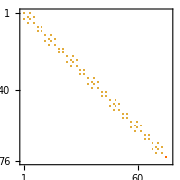
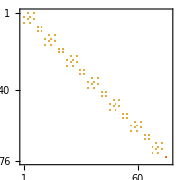
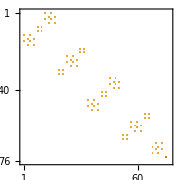
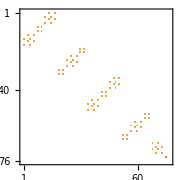
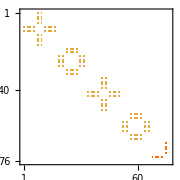
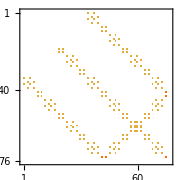
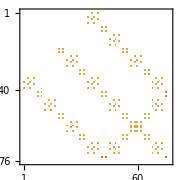
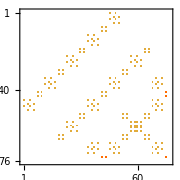

```mathematica
(* Given the action of a line on the traces of the primaries calculate the corresponding twisted hilbert space *)
TwistedSector[s_,z_,defect_]:=Module[
{nz=Position[z, _?(# !=0 &)],st=ConjugateTranspose[s]//N},
st. ReplacePart[z,Thread[nz->defect]] . s//N//Chop//Rationalize
];
MapWithProgress[MatrixPlot[TwistedSector[s,z,#],ImageSize->Small]&,families]//Time
```

## Resolving Ambiguities

As we can see from the answers above for part of the primaries the action of the defects is ambiguous and we really only know the trace. Yet we have a lot of data, perhaps enough to fully constrain the action on the primaries (up to a basis choice). To do this we will use fusion rules. These are highly constrained also simply by looking at the action in the nondegenerate primaries. Then we will search fusion rules for consistencies using a version of BFS.

### Defect Manipulations

Since we don’t need a really big matrix to store the action of the defects, we will instead opt to store them using a list of 1x1 and 2x2 matrices depending on which are ambiguous or not. So we can define an associative operation for the tensor product!!

```mathematica
(* Define a Defect Fusion Product Operation *)
SetAttributes[CircleTimes,{Flat,OneIdentity}]
a_ ⊗ b_:=MapThread[Which[MatrixQ[#1]&&MatrixQ[#2],#1.#2,True,#1*#2]&,{a,b}];
CircleTimes[a_,b_,rest__]:=CircleTimes[CircleTimes[a,b],rest]

(* A couple of helper functions that can be applied to Lines *)
tr[x_]:=Which[MatrixQ[x],Tr[x],True,x];
inv[x_]:=Which[MatrixQ[x],Inverse[x],True,1/x];
dual[x_]:=Which[MatrixQ[x],ConjugateTranspose[x],True,Conjugate[x]];
SuperDagger[x_]:=dual/@x;
ShowLine[L_]:=MatrixForm[MatrixForm/@L];

(* This mask tells us if the current primary is degenerate *)
degMask=Thread[families[[1]]!=1];
degPos=Flatten@Position[degMask,True];
nondegPos=Flatten@Position[Not/@degMask,True];
deg[x_]:=degMask[[x]];
degNum=Total@Boole@degMask;
primNum=Total@Boole@degMask;
famNum=Length@families;
familiesNondeg=families[[All,nondegPos]];degeneracy[i_Integer]:=families[[1,i]];
```

### Invertible Lines

```mathematica
GetInvertibleLines[]:=Module[
{i={{1,0},{0,1}},
a={{1,0},{0,-1}},
b={{0,1},{1,0}},
c={{ⅈ,0},{0,-ⅈ}},
(*c={{0,1},{-1,0}},*)
L1,Lσ,Lχ},
L1={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,i,i,i,i,i,i,i,i,i,i,i,i,i,i};
Lσ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,a,a,a,b,b,a,a,b,b,a,b,b,b,b,a};
Lχ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,a,a,a,c,c,a,a,c,c,a,c,c,c,c,-a};
{L1,Lχ⊗Lχ,Lχ⊗Lσ,Lσ⊗Lχ,Lσ,Lσ⊗Lχ⊗Lχ,Lχ,Lχ⊗Lχ⊗Lχ}
];

(* Extract the invertible Lines *)
Li=GetInvertibleLines[];
L=GetInvertibleLines[];
solvedFamilies=<|
1->{Li[[1]]},
2->{Li[[2]]},
3->Li[[3;;4]],
4->Li[[5;;6]],
5->Li[[7;;8]]
|>;
SolvedQ[x_Integer,solvedFamilies_:solvedFamilies]:=KeyExistsQ[solvedFamilies,x];

(* Takes a list of lines and appends them to the solved families *)
UpdateSolvedLines[lines_]:=
(line|->Module[
{traces=tr/@line,fam},
If[!MemberQ[L,line],
AppendTo[L,line];
fam=First@FirstPosition[N[families],N[traces],Missing,1];
solvedFamilies[fam]=Append[Lookup[solvedFamilies,fam,{}],line];
]
])/@lines;

(* Functions to create a defect with free variables and given traces, as well to extract the variables *)
l[var_Symbol]:=Array[Module[{n=degeneracy[#]},Which[n==1,var[#],True,Table[var[#,n*(i-1) + j],{i,n},{j,n}]]]&,famNum];
(*l[var_Symbol]:=Array[Module[{n=degeneracy[#]},Which[n==1,var[#,1]+ⅈ var[#,2],True,Table[var[#,2n*(i-1) + 2j -1] + ⅈ var[#,2n*(i-1) + 2j],{i,n},{j,n}]]]&,famNum];*)
l[traces_List,var_]:=MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[#2],mat=#2},mat[[n,n]]=#1-Tr[mat[[;;n-1,;;n-1]]];mat ]]&,{traces,l[var]},1];
```

### Gauge Fixing

```mathematica
(* Obtain a general Gauge Transformation that preserves the solved Lines *)
GetGeneralGaugeTransform[L_,var_:P]:=Module[{Lp,LpInvertibleQ,Lpp},
(* Build a General Gauge Transformation *)
Lp=l[var](*Array[Which[!deg[#],1,deg[#],{{var[#,1] ,var[#,2] },{var[#,3],var[#,4]}}]&,famNum]*);
Lp=(Lp //.{ToRules[Reduce[And@@Thread[Flatten[(Lp⊗# -#⊗Lp)&/@L]==0],Backsubstitution->True]]});
Lpp=Variables[Lp];

(* Checks if Lp is invertible for a given numerical set of P variables *)
Module[{
vars=Table[Unique["p"],Length@Lpp],
invertibleLp=And@@((Simplify@Not@Reduce[Or@@(Which[MatrixQ[#],Det[#]==0,True,#==0]&/@#)])&/@Lp)
},
invertibleLp=invertibleLp/.Thread[Lpp->vars];
LpInvertibleQ:=Function@@{vars,Simplify[Evaluate[invertibleLp]]}
];
{Lp,Lpp,LpInvertibleQ}
];
{Lp,Lpp,LpInvertibleQ}=GetGeneralGaugeTransform[L,P];
```

Part::partw: Part 13 of {1,1,1,1,1,1,1,1,1,1,1,1} does not exist.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of …; dimensions are 13 and 39.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of …; dimensions are 39 and 13.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of …; dimensions are 13 and 39.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

ReplaceRepeated::reps: {ToRules[Reduce[MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0,Backsubstitution→True]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

ReplaceRepeated::reps: {ToRules[Reduce[MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0&&MapThread[«1»&,{«2»}]-MapThread[«2»]==0,Backsubstitution→True]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

General::stop: Further output of Reduce::nsmet will be suppressed during this calculation.

ReplaceRepeated::reps: {!Reduce[ToRules[Reduce[Equal[«2»]&&Equal[«2»]&&Equal[«2»]&&Equal[«2»]&&Equal[«2»]&&Equal[«2»]&&Equal[«2»]&&Equal[«2»],Backsubstitution→True]]==0]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

```mathematica
(* These are Queries for if a line is related by conjugation of invertible defects, or by a change of Gauge, or both *)
Clear[conjugateOrbit,invertibleOrbit,fusionOrbit,bilinearFusionOrbit];
conjugateOrbit[x_,Li_:Li]:=conjugateOrbit[x,Li]=DeleteDuplicates[Simplify[#⊗x⊗(inv/@#)]&/@Li];
fusionOrbit[x_,L_:L]:=fusionOrbit[x,L]=DeleteDuplicates[Simplify[#⊗x&/@L]];
bilinearFusionOrbit[x_,L_:L]:=bilinearFusionOrbit[x,L]=DeleteDuplicates[Simplify[Flatten[Outer[#1⊗x⊗#2&,L,L,1,1],1]]];
invertibleOrbit[x_,Li_:Li]:=invertibleOrbit[x,Li]=Module[
{trace=Chop@N[tr/@x]},
Select[bilinearFusionOrbit[x,Li],trace == Chop@N[tr/@#]&]
];

(* Given a Matrix for a gauge transformation this calculates traceless Lie Algebra generators *)
LieGenerators[x_]:=Which[MatrixQ[x],Module[
{II=IdentityMatrix[Length[x]],vars=Variables[x]},
DeleteCases[#-Tr[#]/2 II&/@(D[x,#]&/@vars),0*II]
],True,{}];

(* Takes a defect x and a parameterized Gauge Transformation Lp and returns the relations needed to put x in a fixed gauge *)
GaugeFixingRelations[x_,Lp_:Lp[[1]]]:=Simplify@And@@MapThread[{A,P}|->Module[
{generators=LieGenerators[P]},
Which[!MatrixQ[A],True,
generators==={},True,
DiagonalMatrixQ[P]&&SameQ@@Diagonal[P],True,
MatrixQ[P]&&DiagonalMatrixQ[P],Reduce[And@@Flatten[Table[If[i!=j,A[[i,j]]==A[[j,i]],Nothing],{i,Length[A]},{j,Length[A]}]]],
True,Reduce[Thread[(Tr[ConjugateTranspose[#].A]&/@generators)==0]]]],{x,Lp}];

GaugeFixingRelations[x_,Lp_:Lp[[1]]]:=GroebnerBasis@(Join@@MapThread[{A,P}|->Module[
{},
Which[!MatrixQ[P],{},
DiagonalMatrixQ[P]&&SameQ@@Diagonal[P],{},
DiagonalMatrixQ[P],Expand[{A[[1,2]]*(1-A[[1,2]]),(1-A[[1,2]])*A[[2,1]]*(1-A[[2,1]])}],
True,{}]],{x,Lp}]);

(* Spits out a Defect after we have gaugefixed a bunch of parameters *)
GaugeFix[x_,Lp_:Lp[[1]]]:=(x/.Solve[GaugeFixingRelations[x,Lp]])[[1]];
lGaugeFixed[var_Symbol,Lp_List:Lp]:=GaugeFix[l[var],Lp[[1]]];
lGaugeFixed[traces_List,var_Symbol,Lp_List:Lp]:=GaugeFix[l[traces,var],Lp[[1]]];
```

### Orbit Fixing

```mathematica
(* Given a function f and a group G, checks if f(G A G) == f(A) *)
OuterG[G_]:=OuterG[G]=DeleteDuplicates[Tuples[{G,G}]];
CheckInvariant[f_,A_,G_]:=AllTrue[OuterG[G],Expand[f[A]-f[#[[1]].A.#[[2]]]]===0&];
CheckInvariantFast[m_,orbitSubstitutions_]:=AllTrue[orbitSubstitutions,Expand[m-(m/.#)]===0&];
InvariantMonomialsFast[A_,G_,upToOrder_]:=InvariantMonomialsFast[A,G,upToOrder]=Module[
{vars=Variables[A],Aflat=Flatten[A],monomials,orbitSubstitutions},
monomials=DeleteCases[MonomialList[(1+Total[vars])^upToOrder],1];
orbitSubstitutions=Thread[Aflat->Flatten[#]]&/@((#[[1]].A.#[[2]]) &/@ OuterG[G]);
Sort[Select[monomials,CheckInvariantFast[#,orbitSubstitutions]&]]
];

(* Obtain symbolic expresssions for a generating set of invariants under the orbit of some lines *)
(* Optimization: Have Z-Solve solve the bigger matrix instead *)
Needs["math4ti2`"];
ClearAll[OrbitInvariantsSingle,OrbitInvariants];
OrbitInvariantsSingle[A_,G_,upToOrder_]:=OrbitInvariantsSingle[A,G,upToOrder]=Module[
{vars =Variables[A],Aformal=Array[a,Dimensions[A]],Aflat=Flatten[A],invariantMonomials,exponents,basis},
(* Calculate a lot of monomials in the variables of A, and find which ones are invariant under the group action *)
invariantMonomials=InvariantMonomialsFast[Aformal,G,upToOrder]//.Thread[Flatten[Aformal]->Aflat];

(* Solve for the minimum algebraically independent polynomials by finding a Hilbert basis on the exponents *)
exponents=Exponent[#, vars]&/@invariantMonomials;
basis=math4ti2`hilbert[exponents][[1]];

(* Convert Back to symbols *)
Times @@@(vars^#&/@basis)
];

OrbitInvariants[x_,defects_,upToOrder_Integer:4]:=OrbitInvariants[x,defects,upToOrder]=MapThread[{A,G}|->Which[MatrixQ[A],OrbitInvariantsSingle[A,G,upToOrder],True,{}]
,{x,Transpose[defects]}];
```

### Complex Orbit Fixing

```mathematica
ClearAll[InvariantMonomialsMixed,OrbitInvariantsSingleMixed,OrbitInvariantsMixed];
InvariantMonomialsMixed[A_,Ac_,G_,upToOrder_]:=InvariantMonomialsMixed[A,Ac,G,upToOrder]=Module[
{vars=Join[Variables[A],Variables[Ac]],Aflat=Flatten[A],Acflat=Flatten[Ac],monomials,orbitSubstitutions},
monomials=DeleteCases[MonomialList[(1+Total[vars])^upToOrder],1];
orbitSubstitutions=Thread[Join[Aflat,Acflat]->Join[Flatten[#[[1]].A.#[[2]]],Flatten[Conjugate[#[[1]]].Ac.Conjugate[#[[2]]]]]]&/@OuterG[G];
Sort[Select[monomials,CheckInvariantFast[#,orbitSubstitutions]&]]
];

OrbitInvariantsSingleMixed[A_,Ac_,G_,upToOrder_]:=OrbitInvariantsSingleMixed[A,Ac,G,upToOrder]=Module[
{vars=Join[Variables[A],Variables[Ac]],Aformal=Array[a,Dimensions[A]],Acformal=Array[b,Dimensions[A]],invariantMonomials,exponents,basis},
invariantMonomials=InvariantMonomialsMixed[Aformal,Acformal,G,upToOrder]//.Join[Thread[Flatten[Aformal]->Flatten[A]],Thread[Flatten[Acformal]->Flatten[Ac]]];

exponents=Exponent[#,vars]&/@invariantMonomials;
basis=math4ti2`hilbert[exponents][[1]];
Times@@@(vars^#&/@basis)
];

OrbitInvariantsMixed[x_,xc_,defects_,upToOrder_Integer:4]:=OrbitInvariantsMixed[x,xc,defects,upToOrder]=MapThread[
{A,Ac,G}|->Which[
MatrixQ[A],
OrbitInvariantsSingleMixed[A,Ac,G,upToOrder],
True,
{}
],
{x,xc,Transpose[defects]}
];
```

### Search Fusion Rules

Since we can obtain some partial information for the fusion rules among defects belonging to each family we can extract and list them in the following

```mathematica
(* Takes a matrix M and a vector v and finds all possible nonnegative integer combinations of rows of M that sum to v *)
FindIntegerCombinations[M_,v_]:=Module[
{n=Length[M],m=Length[v],MT=Transpose[N[M]],ubounds, enumerate,results={}},

(* Use linear programming to estimate the maximum number a row can be added in a solution for v *)
ubounds=Table[Module[{sol},
sol=Quiet[LinearProgramming[-UnitVector[n,i],MT,Transpose[{N[v],ConstantArray[0,m]}],ConstantArray[0,n]]];
If[VectorQ[sol],Max[0,sol[[i]]//Chop//RootApproximant],sol]]
,{i,n}];

(* Explore the rest recursively until you hit zero *)
enumerate[rem_,idx_,current_]:=Which[idx>n,If[Chop[N[rem]]==ConstantArray[0,m],AppendTo[results,current]],True,Do[enumerate[rem-k*M[[idx]],idx+1,Append[current,k]],{k,0,ubounds[[idx]]}]];
enumerate[v,1,{}];
results
];
Clear[FindIntegerCombinationsCached];
FindIntegerCombinationsCached[M_,v_]:=FindIntegerCombinationsCached[M,v]=FindIntegerCombinations[M,v];
```

## Solving with Existing Lines

As we keep going through families with higher and higher quantum dimension we can use existing lines to constrain new ones. This is a variation of constrain with invertible lines, but this time it uses the full might of the already solved families. We will do an extra optimization. Since once a family is solved we know all the lines there and not just the traces,  this places a much stricter constraint on what the results of fusions can be other than their traces.

```mathematica
(* Find possible integer combinations for a defect with unknown variables *)
PossibleSimpleDecompositions[trace_]:=Module[
{vars=Variables[trace],indices},
Which[
Length[vars]==0,
FindIntegerCombinationsCached[families,trace],
True,
indices=Flatten@Position[trace, _?(FreeQ[#,Alternatives@@vars]&),{1},Heads->False];
FindIntegerCombinationsCached[families[[All,indices]],trace[[indices]]]
]
];

(* Uses trace equations and known lines to produce candidates for the unknown parameters *)
ReduceDecompositions[defect_,trace_,decompositions_]:=(decomp|->Module[
{sparseDecomp=SparseArray[decomp],indices},
indices=sparseDecomp["NonzeroPositions"][[All,1]];
Which[
(* If the fusion is in one family and it has been solved equate them cell by cell *)
And[Length[indices]==1,SolvedQ[indices[[1]]]],
MapThread[Expand[#1-#2]&,{Flatten[defect],Flatten[#]}]&/@solvedFamilies[indices[[1]]],
(* Otherwise equate their traces *)
True,
{MapThread[Expand[#1-#2]&,{trace,decomp.families},1]}
]])/@decompositions;

CommonSubstitutions[constaints_]:=Module[
{fixedValues=Select[#,(Length@Variables[#]==1&&Exponent[#,First@Variables[#]]==1 &)]&/@constraints},
First@Solve@Thread[(Intersection@@fixedValues)==0]
];

GroebnerBlockReduce[polys_,vars_]:=Flatten[GroebnerBasis/@(List@@GroupBy[DeleteCases[polys,0],First/@Variables[#]&])];

ConstraintsFromKnown[defect_,L_:L,substitutions_:{}]:=Module[
{reducedDefect=defect/.substitutions,vars,products,traces,decompositions},
vars=Variables[reducedDefect];

(* Calculate the possible fusion channels with the known defects *)
products=bilinearFusionOrbit[reducedDefect,L];
traces=tr/@#&/@products;
decompositions=PossibleSimpleDecompositions/@traces;
decompositions=Join@@@MapThread[ReduceDecompositions,{products, traces, decompositions}];

(* Obtain a system of equations and reduce it *)
SortBy[DeleteDuplicates[Sort/@Map[GroebnerBasis[#,vars]&,decompositions,{2}]],Length]
]

(* Constrain using fusion with their dual *)
ConstraintsFromDualFusion[defect_,Li_:Li,substitutions_:{}]:=Module[
{reducedDefect=defect/.substitutions,vars,products,traces,decompositions},
vars=Variables[reducedDefect];

(* Calculate Fusion among members of family *)
products=DeleteDuplicates[Assuming[Thread[vars ∈Reals] ,Simplify[{reducedDefect⊗(SuperDagger[reducedDefect])-Li[[1]],(SuperDagger[reducedDefect])⊗ reducedDefect-Li[[1]]}]]];
traces=tr/@#&/@products;

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
decompositions=PossibleSimpleDecompositions/@traces;
decompositions=Join@@@MapThread[ReduceDecompositions,{products, traces, decompositions}];(*/.Conjugate[var[i_,j_]]:>StringJoin[ToString[var],"c"][i,j];*)
Echo[decompositions];

(* Obtain a system of equations and reduce it *)
SortBy[DeleteDuplicates[Sort/@Map[GroebnerBasis[#,vars]&,decompositions,{2}]],Length]
];

(* Constrain using fusion with themselves *)
ConstraintsFromSelfFusion[defect_,Li_:Li,substitutions_:{}]:=Module[
{reducedDefect=defect/.substitutions,vars,products,traces,decompositions},
vars=Variables[reducedDefect];

(* Calculate Fusion among members of family *)
products={Expand[reducedDefect⊗ reducedDefect]};
traces=tr/@#&/@products;

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
decompositions=PossibleSimpleDecompositions/@traces;
decompositions=Join@@@MapThread[ReduceDecompositions,{products, traces, decompositions}];

(* Obtain a system of equations and reduce it *)
SortBy[DeleteDuplicates[Sort/@Map[GroebnerBasis[#,vars]&,decompositions,{2}]],Length]
];

(* Given some constraints from some fusion combine it with the existing ones or prune if needed *)
Fuse[fusion_,constraints_,vars_,invariants_,varsinv_]:=
Map[First,GatherBy[
DeleteCases[
Flatten[Outer[GroebnerBasis[Join[##],vars]&,constraints,fusion,1,1],1],
{1}
],
c|->PolynomialReduce[#,c,vars][[2]]&/@invariants
(*Echo[GroebnerBasis[Join[#,invariants],varsinv,vars]]&*)
]
];

ReduceConstraints[fusions_,constraints_,vars_,invariants_,varsinv_]:= Module[
{result, singleFusionConstraints=GroebnerBasis[Flatten@Select[fusions,Length[#]==1&],vars],remainingFusions=Select[fusions,Length[#]!=1&]},
result=DeleteCases[GroebnerBasis[Join[#,singleFusionConstraints],vars]&/@constraints,{1}];
Fold[Fuse[#2,#1,vars,invariants,varsinv]&,result,remainingFusions]
]
```

```mathematica
var=x;
SetAttributes[var,NHoldAll];
fam=families[[6]];
def=l[fam,var];
constraints={GaugeFixingRelations[def]};
vars=Variables[def];
defc=Conjugate[def]/.Conjugate[var[i_,j_]]:>StringJoin[ToString[var],"c"][i,j];
varsc=Variables[defc];
invs=Flatten@OrbitInvariants[def,Li];
varsinv=Array[StringJoin["q"],Length@invs];
invsc=Flatten@OrbitInvariantsMixed[def,defc,Li];
varsinvc=Array[StringJoin["qc"],Length@invsc];
fusions=Join[
ConstraintsFromKnown[def,L]//Time,
(*ConstraintsFromDualFusion[def,Li]//Time,*)
(*ConstraintsFromSelfFusion[def,Li]//Time,*)
{}
];
constraints=ReduceConstraints[fusions,constraints,vars,invs-varsinv,varsinv]//Time;
(*fusions=ConstraintsFromSelfFusion[def,Li,CommonSubstitutions[constraints]]//Time;
constraints=ReduceConstraints[fusions,constraints,vars,invs-varsinv,varsinv]//Time;*)
CommonSubstitutions[constraints]
fusions=ConstraintsFromDualFusion[def,Li,CommonSubstitutions[constraints]]//Time
constraints=ReduceConstraints[fusions,constraints,vars,invs-varsinv,varsinv]//Time
```

Part::partw: Part 13 of {1,1,1,1,1,1,1,1,1,1,1,1} does not exist.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1]; dimensions are 12 and 13.

MapThread::mptd: Object MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1] at position {2, 1} in … has only 0 of required 1 dimensions.

Join::heads: Heads Function and List at positions 1 and 2 are expected to be the same.

MapThread::mptd: Object MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1] at position {2, 1} in … has only 0 of required 1 dimensions.

MapThread::mptd: Object MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1] at position {2, 2} in … has only 0 of required 1 dimensions.

MapThread::mptd: Object … at position {2, 1} in … has only 0 of required 1 dimensions.

MapThread::mptd: Object MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1] at position {2, 2} in … has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{1.93185,1.93185,-1.,-1.,0.517638,0.517638,-0.517638,-0.517638,1.,1.,-1.93185,-1.93185},{x[1.],x[2.],x[3.],x[4.],x[5.],x[6.],x[7.],x[8.],x[9.],x[10.],x[11.],x[12.],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1.,x[13.],True,Table[x[13.,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1.].

Transpose::nmtx: The first two levels of … cannot be transposed.

LinearProgramming::lprank12: … must be a vector or a matrix with 2 columns.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{1.93185,1.93185,-1.,-1.,0.517638,0.517638,-0.517638,-0.517638,1.,1.,-1.93185,-1.93185},{x[1.],x[2.],x[3.],x[4.],x[5.],x[6.],x[7.],x[8.],x[9.],x[10.],x[11.],x[12.],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1.,x[13.],True,Table[x[13.,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1.].

Transpose::nmtx: The first two levels of … cannot be transposed.

LinearProgramming::lprank12: … must be a vector or a matrix with 2 columns.

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{1.93185,1.93185,-1.,-1.,0.517638,0.517638,-0.517638,-0.517638,1.,1.,-1.93185,-1.93185},{x[1.],x[2.],x[3.],x[4.],x[5.],x[6.],x[7.],x[8.],x[9.],x[10.],x[11.],x[12.],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1.,x[13.],True,Table[x[13.,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1.].

General::stop: Further output of MapThread::intnm will be suppressed during this calculation.

Transpose::nmtx: The first two levels of … cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

LinearProgramming::lprank12: … must be a vector or a matrix with 2 columns.

General::stop: Further output of LinearProgramming::lprank12 will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1]; dimensions are 12 and 13.

Do::iterb: Iterator {k,0,ubounds$34320⟦1⟧} does not have appropriate bounds.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1]; dimensions are 12 and 13.

Do::iterb: Iterator {k,0,ubounds$34526⟦1⟧} does not have appropriate bounds.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1]; dimensions are 12 and 13.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Do::iterb: Iterator {k,0,ubounds$34637⟦1⟧} does not have appropriate bounds.

General::stop: Further output of Do::iterb will be suppressed during this calculation.

Time:   1.75976

Join::heads: Heads Function and List at positions 1 and 2 are expected to be the same.

MapThread::mptd: Object MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1] at position {2, 1} in … has only 0 of required 1 dimensions.

Time:   0.013837

Intersection::argm: Intersection called with 0 arguments; 1 or more arguments are expected.

{Intersection[]→0}

Intersection::argm: Intersection called with 0 arguments; 1 or more arguments are expected.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Conjugate[Which[!MatrixQ[#2],#1,True,Module[{n=Length[«1»],mat=Slot[«1»]},Part[«3»]=Plus[«2»];mat]]&],{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{Conjugate[x[1]],Conjugate[x[2]],Conjugate[x[3]],Conjugate[x[4]],Conjugate[x[5]],Conjugate[x[6]],Conjugate[x[7]],Conjugate[x[8]],Conjugate[x[9]],Conjugate[x[10]],Conjugate[x[11]],Conjugate[x[12]],Conjugate[Which[{«13»}⟦1,13⟧==1,x[13],True,Table[x[13,Plus[«2»]],{i,n$33880},{j,n$33880}]]]}},1]; dimensions are 12 and 13.

MapThread::mptd: Object MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1] at position {2, 1} in … has only 0 of required 1 dimensions.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Conjugate[Which[!MatrixQ[#2],#1,True,Module[{n=Length[«1»],mat=Slot[«1»]},Part[«3»]=Plus[«2»];mat]]&],{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{Conjugate[x[1]],Conjugate[x[2]],Conjugate[x[3]],Conjugate[x[4]],Conjugate[x[5]],Conjugate[x[6]],Conjugate[x[7]],Conjugate[x[8]],Conjugate[x[9]],Conjugate[x[10]],Conjugate[x[11]],Conjugate[x[12]],Conjugate[Which[{«13»}⟦1,13⟧==1,x[13],True,Table[x[13,Plus[«2»]],{i,n$33880},{j,n$33880}]]]}},1]; dimensions are 12 and 13.

MapThread::mptd: Object MapThread[Conjugate[Which[!MatrixQ[#2],#1,True,Module[{n=Length[«1»],mat=Slot[«1»]},Part[«3»]=Plus[«2»];mat]]&],{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{Conjugate[x[1]],Conjugate[x[2]],Conjugate[x[3]],Conjugate[x[4]],Conjugate[x[5]],Conjugate[x[6]],Conjugate[x[7]],Conjugate[x[8]],Conjugate[x[9]],Conjugate[x[10]],Conjugate[x[11]],Conjugate[x[12]],Conjugate[Which[{«13»}⟦1,13⟧==1,x[13],True,Table[x[13,Plus[«2»]],{i,n$33880},{j,n$33880}]]]}},1] at position {2, 1} in … has only 0 of required 1 dimensions.

RootApproximant::blnotn: The value of the argument Indeterminate in position 1 is not a number.

General::stop: Further output of RootApproximant::blnotn will be suppressed during this calculation.

Do::iterb: Iterator {k,0,ubounds$41080⟦1⟧} does not have appropriate bounds.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Conjugate[Which[!MatrixQ[#2],#1,True,Module[{n=Length[«1»],mat=Slot[«1»]},Part[«3»]=Plus[«2»];mat]]&],{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{Conjugate[x[1]],Conjugate[x[2]],Conjugate[x[3]],Conjugate[x[4]],Conjugate[x[5]],Conjugate[x[6]],Conjugate[x[7]],Conjugate[x[8]],Conjugate[x[9]],Conjugate[x[10]],Conjugate[x[11]],Conjugate[x[12]],Conjugate[Which[{«13»}⟦1,13⟧==1,x[13],True,Table[x[13,Plus[«2»]],{i,n$33880},{j,n$33880}]]]}},1]; dimensions are 12 and 13.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

MapThread::mptd: Object MapThread[Conjugate[Which[!MatrixQ[#2],#1,True,Module[{n=Length[«1»],mat=Slot[«1»]},Part[«3»]=Plus[«2»];mat]]&],{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{Conjugate[x[1]],Conjugate[x[2]],Conjugate[x[3]],Conjugate[x[4]],Conjugate[x[5]],Conjugate[x[6]],Conjugate[x[7]],Conjugate[x[8]],Conjugate[x[9]],Conjugate[x[10]],Conjugate[x[11]],Conjugate[x[12]],Conjugate[Which[{«13»}⟦1,13⟧==1,x[13],True,Table[x[13,Plus[«2»]],{i,n$33880},{j,n$33880}]]]}},1] at position {2, 1} in … has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

{{},{}}

Time:   14.6613

{{}}

MapThread::mptd: Object MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[Slot[«1»]],mat=#2},mat⟦n,n⟧=Slot[«1»]+Times[«2»];mat]]&,{{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-Power[«2»]),-√(2-Power[«2»]),1,1,-√(2+√3),-√(2+√3)},{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12],Which[{{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»},{«12»}}⟦1,13⟧==1,x[13],True,Table[x[13,Times[«2»]+j],{i,n$33880},{j,n$33880}]]}},1] at position {2, 1} in … has only 0 of required 1 dimensions.

Time:   0.009272

{}

```mathematica
mask=Mod[#-1,6]==0&/@Range[6^2];
resolvedCardyStates=Flatten[{1,1}*#&/@(#)]&/@(Pick[#,mask,True]&/@cardyStates);
mask=And[Mod[#-1,2]==0,#<=4*6]&/@Range[4*6+15];
resolvedFamilies=Pick[#,mask,True]&/@families;
```

Pick::incomp: Expressions {1,1,1,1,1,1,1,1,1,1,1,1} and {True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False} have incompatible shapes.

Pick::incomp: Expressions {1,1,-1,-1,1,1,1,1,-1,-1,1,1} and {True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False} have incompatible shapes.

Pick::incomp: Expressions {√2,√2,0,0,-√2,-√2,√2,√2,0,0,-√2,-√2} and {True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False} have incompatible shapes.

General::stop: Further output of Pick::incomp will be suppressed during this calculation.

```mathematica
#*resolvedFamilies[[-13]]&/@resolvedCardyStates//FullSimplify//ToRadicals//MatrixForm
```

cardyStates

```mathematica
resolvedFamilies//MatrixForm
```

(Pick[{1,1,1,1,1,1,1,1,1,1,1,1},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{1,1,-1,-1,1,1,1,1,-1,-1,1,1},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{√2,√2,0,0,-√2,-√2,√2,√2,0,0,-√2,-√2},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{√(2+√3),-√(2-√3),1,-1,√(2-√3),-√(2+√3),√(2+√3),-√(2-√3),1,-1,√(2-√3),-√(2+√3)},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{√(2+√3),√(2+√3),1,1,√(2-√3),√(2-√3),-√(2-√3),-√(2-√3),-1,-1,-√(2+√3),-√(2+√3)},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{√(2+√3),√(2+√3),-1,-1,√(2-√3),√(2-√3),-√(2-√3),-√(2-√3),1,1,-√(2+√3),-√(2+√3)},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{√(2+√3),-√(2-√3),-1,1,√(2-√3),-√(2+√3),√(2+√3),-√(2-√3),-1,1,√(2-√3),-√(2+√3)},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{1+√3,1-√3,0,0,1-√3,1+√3,1+√3,1-√3,0,0,1-√3,1+√3},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{1+√3,1+√3,0,0,1-√3,1-√3,1-√3,1-√3,0,0,1+√3,1+√3},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{2+√3,-1,1,-1,2-√3,-1,-1,2-√3,-1,1,-1,2+√3},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{2+√3,-1,-1,1,2-√3,-1,-1,2-√3,1,-1,-1,2+√3},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{√(2 (7+4 √3)),-√2,0,0,-√(2 (7-4 √3)),√2,-√2,√(2 (7-4 √3)),0,0,√2,-√(2 (7+4 √3))},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True]
Pick[{√(2 (13+4 √3)),√2,0,0,√(2 (13-4 √3)),-√2,√2,-√(2 (13-4 √3)),0,0,-√2,-√(2 (13+4 √3))},{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},True])

```mathematica
II=Array[Which[Abs[i[[#,3]]]==1,1,True,0]&,Length@cardyStates]
sol=(LinearSolve[N@cardyStates,II]//Chop//RootApproximant//ToRadicals)//Simplify
```

{}

RootApproximant::blnotn: The value of the argument LinearSolve[cardyStates,{}] in position 1 is not a number.

RootApproximant[LinearSolve[cardyStates,{}]]

```mathematica
Mod[6,3]
```

0

```mathematica
lines=Select[families,Chop@N[#[[1]]-(1/4 √(1-1/(√5)))^-1]==0&];
lines//MatrixForm
```

{}

```mathematica
lines
```

{}

# OLD

```mathematica
(* Calculates the nullspace of the Jacobian of Lp x - x Lp, and if it is empty then there is no gauge transformation *)
gaugeNullSpace[x_,y_,Lp_:Lp,Lpp_:Lpp]:=gaugeNullSpace[x,y,Lp,Lpp]=(NullSpace@Outer[D,Flatten[ExpandAll[#⊗x-y⊗#]],Lpp])&/@Lp;
GaugeQ[x_,y_,Lp_:Lp,Lpp_:Lpp,LpInvertibleQ_:LpInvertibleQ]:=Module[
{ns,dummies},
ns=gaugeNullSpace[x,y,Lp,Lpp];
Or@@(Which[
#==={},False,
Length@# ===Length@Lpp,True,
True,
dummies=Array[x,Length@#];
Assuming[Thread[Variables[{x,y,dummies}]!=0],Simplify[LpInvertibleQ@@(dummies.#)]]
]&/@ns)];

(* Solves system quietly ignoring the cases when parameters are undetermined *)
QuietSolve[eqn_,vars_]:=Quiet[Solve[eqn,vars],{Solve::svars,Solve::fulldim,Solve::ratnz}];

(* Cleans up some variables *)
CanonicalizeVars[list_]:=Array[i|->Module[{vars},
vars=Variables[list[[i]]];
list[[i]]/.MapIndexed[#->#[[0]][i,#2[[1]]]&,vars]],
Length@list];

(* Given a defect with free variables, it outputs a list of the variables that are pure gauge *)
GaugeParams[x_]:=Module[
{vars=Variables[x]},
Pick[vars,Simplify[GaugeQ[x,x/. #->z]&/@vars,Assumptions->Flatten[{Thread[vars!=0],z!=0}]]]
];
AllGaugeQ[x_]:=Flatten[First/@BooleanVariables[FunctionDomain[Flatten[x],Variables[x]]]]===Flatten[GaugeParams[x]];
```

```mathematica
(* Calculate the invariants for the invertible lines up to Gauge Transformation *)
ll=l[x];
llflat=Flatten[ll];
invertibleInvariants=OrbitInvariants[ll,Li];
InvertibleInvariants=Function[x,invertibleInvariants/.Thread[llflat->Flatten[x]]];
invertibleSyzygies=Syzygies/@invertibleInvariants;

(* Check if two lines are in the same orbit *)
Clear[InvertibleOrbitQ];
InvertibleOrbitQ[x_,y_]:=InvertibleOrbitQ[x,y]=AllTrue[Flatten@Expand[InvertibleInvariants[x]-InvertibleInvariants[y]],#===0&];

(* A solve function that uses orbit fixing to speed things up *)
QuietSolveOrbitFixed[eqns_,orbitInvariants_,vars_]:=Module[
{orbitVars=Array[a,Length@orbitInvariants],orbitEqns,orbitSols,syzygies =Syzygies[orbitInvariants]},

(* Solve the equation in invariant space *)
orbitEqns=GroebnerBasis[
Join[
(List@@eqns)/. Equal[a_,b_]:>a-b,
MapThread[#1-#2&,{orbitInvariants,orbitVars}]
],
orbitVars,
vars,
MonomialOrder->EliminationOrder];

orbitSols= QuietSolve[#==0&/@orbitEqns,orbitVars];

First@QuietSolve[Join[
MapThread[Equal,{orbitVars,orbitInvariants}]/.#,
#==0&/@syzygies
],vars]&/@orbitSols
];
(* Somtimes invariants can be related to each other, this calculates their relations *)
ClearAll[Syzygies];
Syzygies[invariants_]:=Syzygies[invariants]=Module[
{varsGauge=Variables[invariants],vars=Table[Unique["a"],Length@invariants]},
#==0&/@GroebnerBasis[MapThread[Equal,{invariants,vars}],vars,varsGauge]
];

(* A solve function that uses orbit fixing to speed things up *)
QuietSolveOrbitFixed[eqns_,orbitInvariants_,vars_]:=Module[
{reVars=Array[a,Length@vars],imVars=Array[b,Length@vars],compVars,expandRules,orbitVars,invariants,equations,orbitEqns,orbitSols,syzygies},
compVars=Join[reVars,imVars];
expandRules=Thread[vars->reVars+ⅈ imVars];
(*invariants=DeleteCases[Assuming[Thread[compVars∈Reals],Simplify[Join[Re[#],Im[#]]&[ComplexExpand[orbitInvariants/.expandRules]]]],0];*)
invariants=DeleteCases[Assuming[Thread[compVars∈Reals],ComplexExpand[orbitInvariants/.expandRules]],0];
orbitVars=Array[p,Length@invariants];
syzygies =Syzygies[invariants];
equations=DeleteCases[Assuming[Thread[compVars∈Reals],ComplexExpand[Flatten[(List@@@eqns)/. Equal[a_,b_]:>a-b]/.expandRules]],0];

(* Solve the equation in invariant space *)
orbitEqns=GroebnerBasis[
Join[
equations,
MapThread[#1-#2&,{invariants,orbitVars}]
],
orbitVars,
compVars,
MonomialOrder->EliminationOrder];
(*Echo[Thread[orbitVars->invariants],syzygies];
Echo[equations];
Echo[orbitEqns];*)
orbitSols= QuietSolve[#==0&/@orbitEqns,orbitVars];
(First@QuietSolve[Join[
MapThread[Equal,{orbitVars,invariants}]/.#,
#==0&/@syzygies
],compVars]&/@orbitSols)
];
```

```mathematica
ConstrainWithKnown[defect_,L_:L]:=Module[
{vars=Variables[defect],products,traces,decompositions,result},

(* Calculate the possible fusion channels with the known defects *)
products=fusionOrbit[defect,L];
traces=tr/@#&/@products;
decompositions=PossibleSimpleDecompositions/@traces;

(* Obtain a system of equations and reduce it *)
decompositions=Simplify@Reduce/@MapThread[ReduceDecompositions,{products, traces, decompositions}];
(*result=(defect//.#)&/@(QuietSolve[decompositions,vars]);*)
result=DeleteDuplicates[defect//.{Simplify@Reduce/@N[decompositions] //DeleteDuplicates//Reduce//ToRules}];

(* Convert numerical constants back to algebraic form, preserving variables *)
(*result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];*)
result=result/. a_?NumericQ/;!IntegerQ[a]:>ToRadicals@RootApproximant[a];
CanonicalizeVars@DeleteDuplicates[result,InvertibleOrbitQ]
];

(* Convert a boolean expression made up with Ands of Ors of Ands to a collection of vanishing polynomials *)
eqToPoly[Equal[a_,b_]]:=a-b
parseSystem[expr_]:=Module[
{topArgs,flatGens,orBlocks},
(*Unwrap top-level And (or treat single expr as a 1-element list)*)
topArgs=If[Head[expr]===And,List@@expr,{expr}];

(*Flat generators:top-level equalities only*)
flatGens=eqToPoly/@Cases[topArgs,_Equal];
(*OR blocks:each Or becomes a list of per-branch generator lists*)
orBlocks=Map[Function[orExpr,
Map[Function[branch,
Switch[Head[branch],
And,eqToPoly/@Cases[List@@branch,_Equal],
Equal,{eqToPoly[branch]},
True,{},
_,{}
]
],List@@orExpr]],
(*branches of this Or*)
Cases[topArgs,_Or]];
{flatGens,orBlocks}]
```

## Constraining with Dual Fusion

Each defect must fuse with its dual such that it produces the identity. In a unitary representation the dual is given by the conjugate transpose, and therefore we can impose this as a consistency condition as well.

```mathematica
(* Constrain using fusion with their dual *)
ConstrainWithDualFusion[defects_,Li_:Li]:=Module[
{vars=Variables[defects],products,traces,decompositions,orbitInvariants,result},

(* Calculate Fusion among members of family *)
products=Simplify[Flatten[{((#⊗ SuperDagger[#]-Li[[1]])),((SuperDagger[#]⊗ #-Li[[1]]))}&/@defects,1]];
(*Echo[ShowLine/@products];*)
traces=tr/@#&/@products;
(*Echo[ShowLine/@traces];*)

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
decompositions=PossibleSimpleDecompositions/@traces;
(*Echo[decompositions];*)
decompositions=Simplify[MapThread[ReduceDecompositions,{products, traces, decompositions}]]//DeleteDuplicates;
Echo[decompositions];
orbitInvariants=OrbitInvariants[#,Li]&/@defects//Flatten;
Echo[orbitInvariants,"Invariants: "];
result=DeleteDuplicates[Flatten[(defects//.#)&/@(QuietSolveOrbitFixed[And@@decompositions,orbitInvariants,vars]),1]];

(* Convert numerical constants back to algebraic form, preserving variables *)
(*result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];*)
CanonicalizeVars@DeleteDuplicates[Simplify@result,InvertibleOrbitQ]
];
```

## Constraining with Self Fusion

The last condition we will impose is the fusion of the defects among themselves. In particular, if we have a collection of defects, their products should all have fusion decompositions in our fusion ring. This will help us pinpoint the remaining gauge degrees of freedom.

```mathematica
(* Constrain using fusion among thesemeves *)
ConstrainWithSelfFusion[defects_]:=Module[
{vars=Variables[defects],products,traces,decompositions,result},

(* Calculate Fusion among members of family *)
products=DeleteDuplicates[Flatten[Outer[#1⊗#2&,defects,defects,1,1],1]];
traces=tr/@#&/@products;

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
decompositions=PossibleSimpleDecompositions/@traces;
decompositions=MapThread[ReduceDecompositions,{products, traces, decompositions}];
result=Flatten[(defects//.#)&/@(QuietSolve[N[decompositions],vars]),1];

(* Convert numerical constants back to algebraic form, preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[Simplify@result,InvertibleOrbitQ]
];
```

```mathematica
SetAttributes[x,NHoldAll];
fam=families[[6]];
def=lGaugeFixed[fam,x,Lp];
(*ShowLine@def*)
res1=ConstrainWithKnown[def,L]//Simplify//Time;
ShowLine/@res1
res=ConstrainWithDualFusion[res1]//Time;
Echo[Variables[res],"Remaining Variables: "];
ShowLine/@res
```

Reduce::naqs: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} is not a quantified system of equations and inequalities.

Reduce::naqs: … is not a quantified system of equations and inequalities.

General::stop: Further output of Reduce::naqs will be suppressed during this calculation.

ReplaceRepeated::reps: {ToRules[Reduce[{Reduce[Reduce[{{«39»}}]],Reduce[Reduce[{{«39»},{«39»}}]],Reduce[Reduce[{{«39»},{«39»}}]],Reduce[Reduce[{{«39»}}]],Reduce[Reduce[{{«39»}}]],Reduce[Reduce[{{«39»}}]],Reduce[Reduce[{{«39»}}]]}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

ToRules::argx: ToRules called with 2 arguments; 1 argument is expected.

Time:   0.463792

{(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(x[1,1] | x[1,2]
x[1,2] | -x[1,1])
(x[1,3] | x[1,4]
x[1,4] | 2 √2-x[1,3])
(x[1,5] | x[1,6]
x[1,6] | -x[1,5])
(x[1,7] | x[1,8]
x[1,9] | √2-x[1,7])
(x[1,10] | x[1,11]
x[1,12] | √2-x[1,10])
(x[1,13] | x[1,14]
x[1,14] | -x[1,13])
(x[1,15] | x[1,16]
x[1,16] | -2 √2-x[1,15])
(x[1,17] | x[1,18]
x[1,19] | -√2-x[1,17])
(x[1,20] | x[1,21]
x[1,22] | -√2-x[1,20])
(x[1,23] | x[1,24]
x[1,24] | -x[1,23])
(x[1,25] | x[1,26]
x[1,27] | √2-x[1,25])
(x[1,28] | x[1,29]
x[1,30] | √2-x[1,28])
(x[1,31] | x[1,32]
x[1,33] | -√2-x[1,31])
(x[1,34] | x[1,35]
x[1,36] | -√2-x[1,34])
(x[1,37] | x[1,38]
x[1,38] | -x[1,37])),(ToRules[2,1])}

Thread::tdlen: Objects of unequal length in {Conjugate[ToRules[2,1]] ToRules[2,1]}+{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Transpose::nmtx: The first two levels of … cannot be transposed.

LinearProgramming::lprank12: … must be a vector or a matrix with 2 columns.

Do::iterb: Iterator {k,0,ubounds$61906⟦1⟧} does not have appropriate bounds.

{{Conjugate[x[1,2]] x[1,1]==Conjugate[x[1,1]] x[1,2]&&Conjugate[x[1,1]] x[1,1]+Conjugate[x[1,2]] x[1,2]==2&&Conjugate[x[1,4]] x[1,3]+2 √2 x[1,4]==Conjugate[x[1,3]] x[1,4]&&2 √2 Conjugate[x[1,4]]+Conjugate[x[1,3]] x[1,4]==Conjugate[x[1,4]] x[1,3]&&Conjugate[x[1,3]] x[1,3]+Conjugate[x[1,4]] x[1,4]==2&&7+Conjugate[x[1,3]] (-2 √2+x[1,3])+Conjugate[x[1,4]] x[1,4]==1+2 √2 x[1,3]&&Conjugate[x[1,6]] x[1,5]==Conjugate[x[1,5]] x[1,6]&&Conjugate[x[1,5]] x[1,5]+Conjugate[x[1,6]] x[1,6]==2&&Conjugate[x[1,7]] x[1,7]+Conjugate[x[1,8]] x[1,8]==1&&1+Conjugate[x[1,7]] (-√2+x[1,7])+Conjugate[x[1,9]] x[1,9]==√2 x[1,7]&&Conjugate[x[1,10]] x[1,10]+Conjugate[x[1,11]] x[1,11]==1&&1+Conjugate[x[1,10]] (-√2+x[1,10])+Conjugate[x[1,12]] x[1,12]==√2 x[1,10]&&Conjugate[x[1,14]] x[1,13]==Conjugate[x[1,13]] x[1,14]&&Conjugate[x[1,13]] x[1,13]+Conjugate[x[1,14]] x[1,14]==2&&Conjugate[x[1,16]] x[1,15]==(2 √2+Conjugate[x[1,15]]) x[1,16]&&Conjugate[x[1,16]] (2 √2+x[1,15])==Conjugate[x[1,15]] x[1,16]&&Conjugate[x[1,15]] x[1,15]+Conjugate[x[1,16]] x[1,16]==2&&6+2 √2 x[1,15]+Conjugate[x[1,15]] (2 √2+x[1,15])+Conjugate[x[1,16]] x[1,16]==0&&Conjugate[x[1,17]] x[1,17]+Conjugate[x[1,18]] x[1,18]==1&&1+√2 x[1,17]+Conjugate[x[1,17]] (√2+x[1,17])+Conjugate[x[1,19]] x[1,19]==0&&Conjugate[x[1,20]] x[1,20]+Conjugate[x[1,21]] x[1,21]==1&&1+√2 x[1,20]+Conjugate[x[1,20]] (√2+x[1,20])+Conjugate[x[1,22]] x[1,22]==0&&Conjugate[x[1,24]] x[1,23]==Conjugate[x[1,23]] x[1,24]&&Conjugate[x[1,23]] x[1,23]+Conjugate[x[1,24]] x[1,24]==2&&Conjugate[x[1,25]] x[1,25]+Conjugate[x[1,26]] x[1,26]==1&&1+Conjugate[x[1,25]] (-√2+x[1,25])+Conjugate[x[1,27]] x[1,27]==√2 x[1,25]&&Conjugate[x[1,28]] x[1,28]+Conjugate[x[1,29]] x[1,29]==1&&1+Conjugate[x[1,28]] (-√2+x[1,28])+Conjugate[x[1,30]] x[1,30]==√2 x[1,28]&&Conjugate[x[1,31]] x[1,31]+Conjugate[x[1,32]] x[1,32]==1&&1+√2 x[1,31]+Conjugate[x[1,31]] (√2+x[1,31])+Conjugate[x[1,33]] x[1,33]==0&&Conjugate[x[1,34]] x[1,34]+Conjugate[x[1,35]] x[1,35]==1&&1+√2 x[1,34]+Conjugate[x[1,34]] (√2+x[1,34])+Conjugate[x[1,36]] x[1,36]==0&&Conjugate[x[1,38]] x[1,37]==Conjugate[x[1,37]] x[1,38]&&Conjugate[x[1,37]] x[1,37]+Conjugate[x[1,38]] x[1,38]==0&&((Conjugate[x[1,9]] x[1,7]+(√2-Conjugate[x[1,7]]) x[1,8]==ⅈ&&ⅈ+Conjugate[x[1,8]] (√2-x[1,7])+Conjugate[x[1,7]] x[1,9]==0&&Conjugate[x[1,12]] x[1,10]+(√2-Conjugate[x[1,10]]) x[1,11]==ⅈ&&ⅈ+Conjugate[x[1,11]] (√2-x[1,10])+Conjugate[x[1,10]] x[1,12]==0&&Conjugate[x[1,19]] x[1,17]==ⅈ+(√2+Conjugate[x[1,17]]) x[1,18]&&-ⅈ+Conjugate[x[1,18]] (√2+x[1,17])==Conjugate[x[1,17]] x[1,19]&&Conjugate[x[1,22]] x[1,20]==ⅈ+(√2+Conjugate[x[1,20]]) x[1,21]&&-ⅈ+Conjugate[x[1,21]] (√2+x[1,20])==Conjugate[x[1,20]] x[1,22]&&Conjugate[x[1,27]] x[1,25]+(√2-Conjugate[x[1,25]]) x[1,26]==ⅈ&&ⅈ+Conjugate[x[1,26]] (√2-x[1,25])+Conjugate[x[1,25]] x[1,27]==0&&Conjugate[x[1,30]] x[1,28]+(√2-Conjugate[x[1,28]]) x[1,29]==ⅈ&&ⅈ+Conjugate[x[1,29]] (√2-x[1,28])+Conjugate[x[1,28]] x[1,30]==0&&Conjugate[x[1,33]] x[1,31]==ⅈ+(√2+Conjugate[x[1,31]]) x[1,32]&&-ⅈ+Conjugate[x[1,32]] (√2+x[1,31])==Conjugate[x[1,31]] x[1,33]&&Conjugate[x[1,36]] x[1,34]==ⅈ+(√2+Conjugate[x[1,34]]) x[1,35]&&-ⅈ+Conjugate[x[1,35]] (√2+x[1,34])==Conjugate[x[1,34]] x[1,36])||(ⅈ+Conjugate[x[1,9]] x[1,7]+√2 x[1,8]==Conjugate[x[1,7]] x[1,8]&&Conjugate[x[1,8]] (√2-x[1,7])+Conjugate[x[1,7]] x[1,9]==ⅈ&&ⅈ+Conjugate[x[1,12]] x[1,10]+√2 x[1,11]==Conjugate[x[1,10]] x[1,11]&&Conjugate[x[1,11]] (√2-x[1,10])+Conjugate[x[1,10]] x[1,12]==ⅈ&&Conjugate[x[1,19]] x[1,17]==-ⅈ+(√2+Conjugate[x[1,17]]) x[1,18]&&ⅈ+Conjugate[x[1,18]] (√2+x[1,17])==Conjugate[x[1,17]] x[1,19]&&Conjugate[x[1,22]] x[1,20]==-ⅈ+(√2+Conjugate[x[1,20]]) x[1,21]&&ⅈ+Conjugate[x[1,21]] (√2+x[1,20])==Conjugate[x[1,20]] x[1,22]&&ⅈ+Conjugate[x[1,27]] x[1,25]+√2 x[1,26]==Conjugate[x[1,25]] x[1,26]&&Conjugate[x[1,26]] (√2-x[1,25])+Conjugate[x[1,25]] x[1,27]==ⅈ&&ⅈ+Conjugate[x[1,30]] x[1,28]+√2 x[1,29]==Conjugate[x[1,28]] x[1,29]&&Conjugate[x[1,29]] (√2-x[1,28])+Conjugate[x[1,28]] x[1,30]==ⅈ&&Conjugate[x[1,33]] x[1,31]==-ⅈ+(√2+Conjugate[x[1,31]]) x[1,32]&&ⅈ+Conjugate[x[1,32]] (√2+x[1,31])==Conjugate[x[1,31]] x[1,33]&&Conjugate[x[1,36]] x[1,34]==-ⅈ+(√2+Conjugate[x[1,34]]) x[1,35]&&ⅈ+Conjugate[x[1,35]] (√2+x[1,34])==Conjugate[x[1,34]] x[1,36]))},{Conjugate[x[1,2]] x[1,1]==Conjugate[x[1,1]] x[1,2]&&Conjugate[x[1,1]] x[1,1]+Conjugate[x[1,2]] x[1,2]==2&&Conjugate[x[1,4]] x[1,3]+2 √2 x[1,4]==Conjugate[x[1,3]] x[1,4]&&2 √2 Conjugate[x[1,4]]+Conjugate[x[1,3]] x[1,4]==Conjugate[x[1,4]] x[1,3]&&Conjugate[x[1,3]] x[1,3]+Conjugate[x[1,4]] x[1,4]==2&&7+Conjugate[x[1,3]] (-2 √2+x[1,3])+Conjugate[x[1,4]] x[1,4]==1+2 √2 x[1,3]&&Conjugate[x[1,6]] x[1,5]==Conjugate[x[1,5]] x[1,6]&&Conjugate[x[1,5]] x[1,5]+Conjugate[x[1,6]] x[1,6]==2&&1+Conjugate[x[1,7]] (-√2+x[1,7])+Conjugate[x[1,8]] x[1,8]==√2 x[1,7]&&Conjugate[x[1,7]] x[1,7]+Conjugate[x[1,9]] x[1,9]==1&&1+Conjugate[x[1,10]] (-√2+x[1,10])+Conjugate[x[1,11]] x[1,11]==√2 x[1,10]&&Conjugate[x[1,10]] x[1,10]+Conjugate[x[1,12]] x[1,12]==1&&Conjugate[x[1,14]] x[1,13]==Conjugate[x[1,13]] x[1,14]&&Conjugate[x[1,13]] x[1,13]+Conjugate[x[1,14]] x[1,14]==2&&Conjugate[x[1,16]] x[1,15]==(2 √2+Conjugate[x[1,15]]) x[1,16]&&Conjugate[x[1,16]] (2 √2+x[1,15])==Conjugate[x[1,15]] x[1,16]&&Conjugate[x[1,15]] x[1,15]+Conjugate[x[1,16]] x[1,16]==2&&6+2 √2 x[1,15]+Conjugate[x[1,15]] (2 √2+x[1,15])+Conjugate[x[1,16]] x[1,16]==0&&1+√2 x[1,17]+Conjugate[x[1,17]] (√2+x[1,17])+Conjugate[x[1,18]] x[1,18]==0&&Conjugate[x[1,17]] x[1,17]+Conjugate[x[1,19]] x[1,19]==1&&1+√2 x[1,20]+Conjugate[x[1,20]] (√2+x[1,20])+Conjugate[x[1,21]] x[1,21]==0&&Conjugate[x[1,20]] x[1,20]+Conjugate[x[1,22]] x[1,22]==1&&Conjugate[x[1,24]] x[1,23]==Conjugate[x[1,23]] x[1,24]&&Conjugate[x[1,23]] x[1,23]+Conjugate[x[1,24]] x[1,24]==2&&1+Conjugate[x[1,25]] (-√2+x[1,25])+Conjugate[x[1,26]] x[1,26]==√2 x[1,25]&&Conjugate[x[1,25]] x[1,25]+Conjugate[x[1,27]] x[1,27]==1&&1+Conjugate[x[1,28]] (-√2+x[1,28])+Conjugate[x[1,29]] x[1,29]==√2 x[1,28]&&Conjugate[x[1,28]] x[1,28]+Conjugate[x[1,30]] x[1,30]==1&&1+√2 x[1,31]+Conjugate[x[1,31]] (√2+x[1,31])+Conjugate[x[1,32]] x[1,32]==0&&Conjugate[x[1,31]] x[1,31]+Conjugate[x[1,33]] x[1,33]==1&&1+√2 x[1,34]+Conjugate[x[1,34]] (√2+x[1,34])+Conjugate[x[1,35]] x[1,35]==0&&Conjugate[x[1,34]] x[1,34]+Conjugate[x[1,36]] x[1,36]==1&&Conjugate[x[1,38]] x[1,37]==Conjugate[x[1,37]] x[1,38]&&Conjugate[x[1,37]] x[1,37]+Conjugate[x[1,38]] x[1,38]==0&&((Conjugate[x[1,9]] (√2-x[1,7])+Conjugate[x[1,7]] x[1,8]==ⅈ&&ⅈ+Conjugate[x[1,8]] x[1,7]+√2 x[1,9]==Conjugate[x[1,7]] x[1,9]&&Conjugate[x[1,12]] (√2-x[1,10])+Conjugate[x[1,10]] x[1,11]==ⅈ&&ⅈ+Conjugate[x[1,11]] x[1,10]+√2 x[1,12]==Conjugate[x[1,10]] x[1,12]&&Conjugate[x[1,18]] x[1,17]==-ⅈ+(√2+Conjugate[x[1,17]]) x[1,19]&&ⅈ+Conjugate[x[1,19]] (√2+x[1,17])==Conjugate[x[1,17]] x[1,18]&&Conjugate[x[1,21]] x[1,20]==-ⅈ+(√2+Conjugate[x[1,20]]) x[1,22]&&ⅈ+Conjugate[x[1,22]] (√2+x[1,20])==Conjugate[x[1,20]] x[1,21]&&Conjugate[x[1,27]] (√2-x[1,25])+Conjugate[x[1,25]] x[1,26]==ⅈ&&ⅈ+Conjugate[x[1,26]] x[1,25]+√2 x[1,27]==Conjugate[x[1,25]] x[1,27]&&Conjugate[x[1,30]] (√2-x[1,28])+Conjugate[x[1,28]] x[1,29]==ⅈ&&ⅈ+Conjugate[x[1,29]] x[1,28]+√2 x[1,30]==Conjugate[x[1,28]] x[1,30]&&Conjugate[x[1,32]] x[1,31]==-ⅈ+(√2+Conjugate[x[1,31]]) x[1,33]&&ⅈ+Conjugate[x[1,33]] (√2+x[1,31])==Conjugate[x[1,31]] x[1,32]&&Conjugate[x[1,35]] x[1,34]==-ⅈ+(√2+Conjugate[x[1,34]]) x[1,36]&&ⅈ+Conjugate[x[1,36]] (√2+x[1,34])==Conjugate[x[1,34]] x[1,35])||(ⅈ+Conjugate[x[1,9]] (√2-x[1,7])+Conjugate[x[1,7]] x[1,8]==0&&Conjugate[x[1,8]] x[1,7]+(√2-Conjugate[x[1,7]]) x[1,9]==ⅈ&&ⅈ+Conjugate[x[1,12]] (√2-x[1,10])+Conjugate[x[1,10]] x[1,11]==0&&Conjugate[x[1,11]] x[1,10]+(√2-Conjugate[x[1,10]]) x[1,12]==ⅈ&&Conjugate[x[1,18]] x[1,17]==ⅈ+(√2+Conjugate[x[1,17]]) x[1,19]&&-ⅈ+Conjugate[x[1,19]] (√2+x[1,17])==Conjugate[x[1,17]] x[1,18]&&Conjugate[x[1,21]] x[1,20]==ⅈ+(√2+Conjugate[x[1,20]]) x[1,22]&&-ⅈ+Conjugate[x[1,22]] (√2+x[1,20])==Conjugate[x[1,20]] x[1,21]&&ⅈ+Conjugate[x[1,27]] (√2-x[1,25])+Conjugate[x[1,25]] x[1,26]==0&&Conjugate[x[1,26]] x[1,25]+(√2-Conjugate[x[1,25]]) x[1,27]==ⅈ&&ⅈ+Conjugate[x[1,30]] (√2-x[1,28])+Conjugate[x[1,28]] x[1,29]==0&&Conjugate[x[1,29]] x[1,28]+(√2-Conjugate[x[1,28]]) x[1,30]==ⅈ&&Conjugate[x[1,32]] x[1,31]==ⅈ+(√2+Conjugate[x[1,31]]) x[1,33]&&-ⅈ+Conjugate[x[1,33]] (√2+x[1,31])==Conjugate[x[1,31]] x[1,32]&&Conjugate[x[1,35]] x[1,34]==ⅈ+(√2+Conjugate[x[1,34]]) x[1,36]&&-ⅈ+Conjugate[x[1,36]] (√2+x[1,34])==Conjugate[x[1,34]] x[1,35]))},{}}

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of …; dimensions are 1 and 39.

Invariants:   {x[1,1],x[1,2]^2,x[1,3],x[1,4]^2,x[1,5],x[1,6]^2,x[1,7]^2 x[1,8] x[1,9],x[1,10]^2 x[1,11] x[1,12],x[1,13],x[1,14]^2,x[1,15],x[1,16]^2,x[1,17]^2 x[1,18] x[1,19],x[1,20]^2 x[1,21] x[1,22],x[1,23],x[1,24]^2,x[1,25]^2 x[1,26] x[1,27],x[1,28]^2 x[1,29] x[1,30],x[1,31]^2 x[1,32] x[1,33],x[1,34]^2 x[1,35] x[1,36],x[1,37]^2,x[1,38]^2,MapThread[Function[{A$,G$},Which[MatrixQ[A$],OrbitInvariantsSingle[A$,G$,4],True,{}]],{{ToRules[2,1]},{{1,1,1,1,1,1,1,1},{1,1,1,1,-1,-1,-1,-1},{1,1,1,1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,-1,-1,-1,-1},{1,1,1,1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,-1,-1,-1,-1},{1,1,1,1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,-1,-1,-1,-1},{1,1,1,1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1},{1,1,-1,-1,1,1,-1,-1},{1,1,-1,-1,-1,-1,1,1},{1,1,-1,-1,-1,-1,1,1},{1,1,-1,-1,1,1,-1,-1},{1,1,-1,-1,1,1,-1,-1},{1,1,-1,-1,-1,-1,1,1},{1,1,-1,-1,-1,-1,1,1},{1,1,-1,-1,1,1,-1,-1},{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}},{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}},{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}},{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}},{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}},{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}},{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}},{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}},{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}},{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}},{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}},{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}},{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}},{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}},{{{1,0},{0,1}},{{1,0},{0,1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{-1,0},{0,1}},{{-1,0},{0,1}}}}}]}

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of …; dimensions are 1 and 39.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Join::heads: Heads And and List at positions 1 and 2 are expected to be the same.

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and List at positions 1 and 2 are expected to be the same.

Solve::naqs: … is not a quantified system of equations and inequalities.

ReplaceAll::reps: {p[1],p[2],p[3],p[4],p[5],p[6],p[7],p[8],p[9],p[10],p[11],p[12],p[13],p[14],p[15],p[16],p[17],p[18],p[19],p[20],p[21],p[22],p[23]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Solve::naqs: … is not a quantified system of equations and inequalities.

General::stop: Further output of Solve::naqs will be suppressed during this calculation.

ReplaceRepeated::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

Time:   3.3653

Remaining Variables:   {1//.1,2//.1}

ReplaceRepeated::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{1//.1,2//.1}